x direction

## test for zero order

### set up

```mathematica
F0[j_,theta1_,theta2_]:=(bJ)^j/j! Cos[theta1-theta2]^j (Qx0-bmu(Cos[theta1]+Cos[theta2]))
Qx0=0;
Qx1=bmu^2+(bmu^2  BesselI[1,bJ])/BesselI[0,bJ];
```

here j is Taylor expansion coefficient

```mathematica
H0[0,j_,theta1_]:=1/(2Pi)Integrate[F0[j,theta1,theta2],{theta2,0,2Pi}]
H0c[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H0s[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
```

IOcch means:∫_0^(2 π) H0c Cosh[2 Pi-xi]ⅆxi  0CCH etc.. and 0 means zero order of Ε

```mathematica
I0cch[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0csh[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I0sch[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0ssh[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
```

```mathematica
F0s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0sch[n,j,2Pi]+1/(2n)I0ssh[n,j,2Pi]
F0c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0cch[n,j,2Pi]+1/(2n)I0csh[n,j,2Pi]
```

```mathematica
E0s[n_,j_]:=F0s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0ssh[n,j,2Pi]
E0c[n_,j_]:=F0c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0csh[n,j,2Pi]
```

Note the 0 of  A0C(A_0(θ1))  here means zero order of Ε
A0c[0,j,theta1] here is A_0(θ_1) in steven’s sol, this part could be include in ∑_(n=1)^∞ A_n_c Cos(nθ2) so it could start with n=0 i.e. ∑_(n=0)^∞ A_n_c Cos(nθ2) since Cos(nθ2) = 1 for n = 0;

```mathematica
A0c[0,j_,theta1_]:=Integrate[H0[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A0s[0,j_,theta1_]:=0
A0s[n_,j_,theta1_]:=E0s[n,j]Sinh[n theta1]+F0s[n,j]Cosh[n theta1]+1/n I0ssh[n,j,theta1]
A0c[n_,j_,theta1_]:=E0c[n,j]Sinh[n theta1]+F0c[n,j]Cosh[n theta1]+1/n I0csh[n,j,theta1]
```

use Leibniz rule ,dA0S means dA0S/d theta1

```mathematica
dA0c[0,j_,theta1_]:=Integrate[H0[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA0s[0,j_,theta1_]:=0
dA0s[n_,j_,theta1_]:=n E0s[n,j]Cosh[n theta1]+n F0s[n,j]Sinh[n theta1]+I0sch[n,j,theta1]
dA0c[n_,j_,theta1_]:=n E0c[n,j]Cosh[n theta1]+n F0c[n,j]Sinh[n theta1]+I0cch[n,j,theta1]
```

pv10 means P* V_1^E in zero order of Ε
pv20 means P* V_2^E in zero order of Ε

```mathematica
pv10[bJx_,bmux_,xi_,xj_]:=Sum[dA0s[n,j,theta1]Sin[n theta2]+dA0c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,nmax},{j,0,jmax}]
pv20[bJx_,bmux_,xi_,xj_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,1,nmax},{j,0,jmax}]
```

### A0ns and dA0ns from summing j

```mathematica
Ax0[theta1_]:=bmu (BesselI[0,bJ]+BesselI[1,bJ]) (-1+Cos[theta1])
dAx0[theta1_]:=-bmu (BesselI[0,bJ]+BesselI[1,bJ]) Sin[theta1]
```

```mathematica
Axc0[n_,theta1_]:=1/(bJ+4 bJ n^4)2 bmu (((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ]) Cos[theta1] Cos[n theta1]+n (2 bJ BesselI[-1+n,bJ]+(1+2 bJ+2 (-1+n) n) BesselI[n,bJ]) Sin[theta1] Sin[n theta1])
Axc0[0,theta1_]:=bmu (BesselI[0,bJ]+BesselI[1,bJ]) (-1+Cos[theta1])
```

```mathematica
dAxc0[n_,theta1_]:=1/(1+4 n^4)bmu (2 BesselI[n,bJ] (-Cos[n theta1] Sin[theta1]+n (1-2 n^2) Cos[theta1] Sin[n theta1])+BesselI[-1+n,bJ] ((1+n) Sin[(-1+n) theta1]+2 n^3 Sin[theta1-n theta1])+(-1+n-2 n^3) BesselI[1+n,bJ] Sin[theta1+n theta1])
dAxc0[0,theta1_]:=-bmu (BesselI[0,bJ]+BesselI[1,bJ]) Sin[theta1]
```

```mathematica
Axs0[n_,theta1_]:=1/(1+4 n^4)bmu ((1+2 n (1+n)) BesselI[-1+n,bJ] Sin[(-1+n) theta1]+2 BesselI[n,bJ] (-2 n Cos[n theta1] Sin[theta1]+(1+2 n^2) Cos[theta1] Sin[n theta1])+(1+2 (-1+n) n) BesselI[1+n,bJ] Sin[theta1+n theta1])
Axs0[0,theta1_]:=0
```

```mathematica
dAxs0[n_,theta1_]:=1/(bJ+4 bJ n^4)(-2 bmu n (BesselI[n,bJ]+(-1+2 n^2) (-bJ BesselI[-1+n,bJ]+(-bJ+n) BesselI[n,bJ])) Cos[theta1] Cos[n theta1]-2 bmu (bJ BesselI[-1+n,bJ]+(bJ+n (-1+n-2 n^3)) BesselI[n,bJ]) Sin[theta1] Sin[n theta1])
dAxs0[0,theta1_]:=0
```

Axs0 is tested

### Import zero order

#### H0ns

```mathematica
H0x=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/H0x.xls"],1];
Table[H0[0,j_,xi_]:=ToExpression[H0x[[j+1,2]]]/.theta1->xi,{j,0,10}];
```

```mathematica
H0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/H0cx.xls"],1];
Table[H0c[n_,j_,xi_]:=ToExpression[H0cx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
H0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/H0sx.xls"],1];
Table[H0s[n_,j_,xi_]:=ToExpression[H0sx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### I0cch

```mathematica
I0cchx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/I0cchx.xls"],1];
Table[I0cch[n_,j_,xi_]:=ToExpression[I0cchx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0schx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/I0schx.xls"],1];
Table[I0sch[n_,j_,xi_]:=ToExpression[I0schx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0cshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/I0cshx.xls"],1];
Table[I0csh[n_,j_,xi_]:=ToExpression[I0cshx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0sshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/I0sshx.xls"],1];
Table[I0ssh[n_,j_,xi_]:=ToExpression[I0sshx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### F0ns

```mathematica
F0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/F0sx.xls"],1];
Table[F0s[n_,j_]:=ToExpression[F0sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
F0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/F0cx.xls"],1];
Table[F0c[n_,j_]:=ToExpression[F0cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

#### E0ns

```mathematica
E0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/E0sx.xls"],1];
Table[E0s[n_,j_]:=ToExpression[E0sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/E0cx.xls"],1];
Table[E0c[n_,j_]:=ToExpression[E0cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

#### A0n and dA0n

```mathematica
A0cx0=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/A0cx0.xls"],1];
A0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/A0cx.xls"],1];
Table[A0c[0,j_,theta1_]:=ToExpression[A0cx0[[j+1,2]]],{j,0,10}];
Table[A0c[n_,j_,theta1_]:=ToExpression[A0cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
A0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/A0sx.xls"],1];
A0s[0,j,theta1]:=0;
Table[A0s[n_,j_,theta1_]:=ToExpression[A0sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA0cx0=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/dA0cx0.xls"],1];
dA0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/dA0cx.xls"],1];
Table[dA0c[0,j_,theta1_]:=ToExpression[dA0cx0[[j+1,2]]],{j,0,10}];
Table[dA0c[n_,j_,theta1_]:=ToExpression[dA0cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
ToExpression[dA0cx0[[1+1,2]]]
dA0c[0,1,theta1]
```

-0.5 Sin[theta1]

-0.5 Sin[theta1]

```mathematica
Table[ToExpression[dA0cx0[[j+1,2]]],{j,0,10}]
```

{-1. Sin[theta1],-0.5 Sin[theta1],-0.25 Sin[theta1],-0.0625 Sin[theta1],-0.015625 Sin[theta1],-0.00260417 Sin[theta1],-0.000434028 Sin[theta1],-0.0000542535 Sin[theta1],-6.78168×10^-6 Sin[theta1],-6.78168×10^-7 Sin[theta1],-6.78168×10^-8 Sin[theta1]}

```mathematica
dA0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/dA0sx.xls"],1];
dA0s[0,j,theta1]:=0;
Table[dA0s[n_,j_,theta1_]:=ToExpression[dA0sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

### test for Hns

#### H0

```mathematica
(*H0nNumerical[bJ_,bmu_,theta1_]:=NIntegrate[Exp[bJ Cos[theta1-theta2]] (0-bmu(Cos[theta1]+Cos[theta2])),{theta2,0,2Pi}]/2/Pi*)
```

```mathematica
(*bmu=RandomReal[{1,10}]
bJ=RandomReal[{1,10}]
(*t13=Sum[H0[0,j,theta1],a{j,0,3}];
t16=Sum[H0[0,j,theta1],{j,0,6}];
t110=Sum[H0[0,j,theta1],{j,0,10}];*)
aH0=bmu (-BesselI[0,bJ]-BesselI[1,bJ])Cos[theta1];
Plot[{aH0*1.05,H0nNumerical[bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->{"J3","J6","J10","Analytical"}]*)
```

#### H0c

```mathematica
(*HcnNumerical[n_,bJ_,bmu_,theta1_]:=NIntegrate[Cos[n theta2]Exp[bJ Cos[theta1-theta2]] (0-bmu(Cos[theta1]+Cos[theta2])),{theta2,0,2Pi}]/Pi
bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
aH0c[n_]:=-bmu((BesselI[n-1,betaJ]+BesselI[n,betaJ])Cos[(n-1)theta1]+(BesselI[n+1,betaJ]+BesselI[n,betaJ])Cos[(n+1)theta1])/.betaJ->bJ
Plot[{aH0c[1]*1.05,HcnNumerical[1,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{aH0c[3]*1.05,HcnNumerical[3,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{aH0c[5]*1.05,HcnNumerical[5,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

```mathematica
(**)
```

```mathematica
(**)
```

#### H0s

```mathematica
(*HsnNumerical[n_,bJ_,bmu_,theta1_]:=NIntegrate[Sin[n theta2]Exp[bJ Cos[theta1-theta2]] (0-bmu(Cos[theta1]+Cos[theta2])),{theta2,0,2Pi}]/Pi
bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
aH0s[n_]:=-bmu((BesselI[n-1,betaJ]+BesselI[n,betaJ])Sin[(n-1)theta1]+(BesselI[n+1,betaJ]+BesselI[n,betaJ])Sin[(n+1)theta1])/.betaJ->bJ
Plot[{aH0s[1]*1.05,HsnNumerical[1,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{aH0s[3]*1.05,HsnNumerical[3,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{aH0s[5]*1.05,HsnNumerical[5,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

### test for F0ns and E0ns

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

```mathematica
(*1/(bJ+4 bJ n^4)2 betaMu ((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ])/.betaMu->bmu*)
```

```mathematica
(*1/(bJ+4 bJ n^4)2 bmu ((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ])-1/(bJ+4 bJ n^4)2 bmu ((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ])//Simplify*)
```

```mathematica
(*F0cn[n_]:=1/(bJ+4 bJ n^4)2 bmu ((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ]);*)
```

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];*)
```

value start to change for bJ get biggers

```mathematica
(*bmu=100;bJ=5;
Print["bmu = ",bmu," ,bJ= " , bJ];
Sum[F0c[1,j],{j,0,9}]//N
F0cn[1]//N
Sum[F0c[3,j],{j,0,9}]//N
F0cn[3]//N
Sum[F0c[5,j],{j,0,9}]//N
F0cn[5]//N
*)
```

bmu = 100 ,bJ= 5

bmu = 100 ,bJ= 5

```mathematica
(*5940.359355785228 *)
```

```mathematica
(*Table[F0s[n,j],{n,1,5},{j,0,10}]*)
```

```mathematica
(*1/(bJ+4 bJ n^4)2 betaMu (-BesselI[n,bJ]+(-1+2 n^2) (bJ BesselI[-1+n,bJ]+(bJ-n) BesselI[n,bJ]))/.betaMu->bmu*)
```

```mathematica
(*E0sn[n_]:=1/(bJ+4 bJ n^4)2 bmu (-BesselI[n,bJ]+(-1+2 n^2) (bJ BesselI[-1+n,bJ]+(bJ-n) BesselI[n,bJ]))*)
```

does not agree!!

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
Sum[E0s[1,j],{j,0,10}]//N
E0sn[1]//N
Sum[E0s[3,j],{j,0,10}]//N
E0sn[3]//N
Sum[E0s[5,j],{j,0,10}]//N
E0sn[5]//N*)
```

```mathematica
(*Table[E0c[n,j],{n,1,5},{j,0,10}]*)
```

### test for A0ns

#### Ax0 and dAx0

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{1,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
Ax0=bmu (BesselI[0,bJ]+BesselI[1,bJ]) (-1+Cos[theta1]);
Ax0Sum=Sum[A0c[0,j,theta1],{j,0,10}];
Plot[{Ax0,Ax0Sum},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

```mathematica
(*Sum[A0c[0,j,theta1],{j,0,10}]*)
```

```mathematica
(*dAx0=-bmu (BesselI[0,bJ]+BesselI[1,bJ]) Sin[theta1];
dAx0Sum=Sum[dA0c[0,j,theta1],{j,0,10}];
Plot[{dAx0,dAx0Sum},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

#### Axcn and dAxcn

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{1,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

```mathematica
(*
Axcn[n_]:=1/(bJ+4 bJ n^4)2 bmu (((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ]) Cos[theta1] Cos[n theta1]+n (2 bJ BesselI[-1+n,bJ]+(1+2 bJ+2 (-1+n) n) BesselI[n,bJ]) Sin[theta1] Sin[n theta1])
AxcnSum1=Sum[A0c[1,j,theta1],{j,0,10}];
AxcnSum3=Sum[A0c[3,j,theta1],{j,0,10}];
AxcnSum5=Sum[A0c[5,j,theta1],{j,0,10}];
Plot[{AxcnSum1,Axcn[1]},{theta1,0,2Pi},PlotLegends->Automatic];
Plot[{AxcnSum3,Axcn[3]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{AxcnSum5,Axcn[5]},{theta1,0,2Pi},PlotLegends->Automatic];*)
```

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{1,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

```mathematica
(*
dAxcn[n_]:=1/(1+4 n^4)bmu (2 BesselI[n,bJ] (-Cos[n theta1] Sin[theta1]+n (1-2 n^2) Cos[theta1] Sin[n theta1])+BesselI[-1+n,bJ] ((1+n) Sin[(-1+n) theta1]+2 n^3 Sin[theta1-n theta1])+(-1+n-2 n^3) BesselI[1+n,bJ] Sin[theta1+n theta1])
dAxcnSum1=Sum[dA0c[1,j,theta1],{j,0,10}];
dAxcnSum3=Sum[dA0c[3,j,theta1],{j,0,10}];
dAxcnSum5=Sum[dA0c[5,j,theta1],{j,0,10}];
Plot[{dAxcnSum1,dAxcn[1]},{theta1,0,2Pi},PlotLegends->Automatic];
Plot[{dAxcnSum3,dAxcn[3]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{dAxcnSum5,dAxcn[5]},{theta1,0,2Pi},PlotLegends->Automatic];*)
```

#### Axsn and dAxsn

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{1,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

```mathematica
(*
Print["bmu = ",bmu," ,bJ= " , bJ]
Axsn[n_]:=1/(1+4 n^4)bmu ((1+2 n (1+n)) BesselI[-1+n,bJ] Sin[(-1+n) theta1]+2 BesselI[n,bJ] (-2 n Cos[n theta1] Sin[theta1]+(1+2 n^2) Cos[theta1] Sin[n theta1])+(1+2 (-1+n) n) BesselI[1+n,bJ] Sin[theta1+n theta1]);
AxsnSum1=Sum[A0s[1,j,theta1],{j,0,10}];
AxsnSum3=Sum[A0s[3,j,theta1],{j,0,10}];
AxsnSum5=Sum[A0s[5,j,theta1],{j,0,10}];
Plot[{AxsnSum1,Axsn[1],Axsn[1]*1.05},{theta1,0,2Pi},PlotLegends->Automatic];
Plot[{AxsnSum3,Axsn[3],Axsn[3]*1.05},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{AxsnSum5,Axsn[5],Axsn[5]*1.05},{theta1,0,2Pi},PlotLegends->Automatic];*)
```

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{1,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

```mathematica
(*dAxsn[n_]:=1/(bJ+4 bJ n^4)(-2 bmu n (BesselI[n,bJ]+(-1+2 n^2) (-bJ BesselI[-1+n,bJ]+(-bJ+n) BesselI[n,bJ])) Cos[theta1] Cos[n theta1]-2 bmu (bJ BesselI[-1+n,bJ]+(bJ+n (-1+n-2 n^3)) BesselI[n,bJ]) Sin[theta1] Sin[n theta1]);
dAxsnSum1=Sum[dA0s[1,j,theta1],{j,0,10}];
dAxsnSum3=Sum[dA0s[3,j,theta1],{j,0,10}];
dAxsnSum5=Sum[dA0s[5,j,theta1],{j,0,10}];
Plot[{dAxsnSum1,dAxsn[1]},{theta1,0,2Pi},PlotLegends->Automatic];
Plot[{dAxsnSum3,dAxsn[3]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{dAxsnSum5,dAxsn[5]},{theta1,0,2Pi},PlotLegends->Automatic];*)
```

```mathematica
(*A0sxn[n_]:=1/(1+4 n^4)bmu ((1+2 n (1+n)) BesselI[-1+n,bJ] Sin[(-1+n) theta1]+2 BesselI[n,bJ] (-2 n Cos[n theta1] Sin[theta1]+(1+2 n^2) Cos[theta1] Sin[n theta1])+(1+2 (-1+n) n) BesselI[1+n,bJ] Sin[theta1+n theta1])*)
```

```mathematica
(*Sum[A0sx[1,j,theta1],{j,0,10}];//Simplify
*)
```

```mathematica
(*bmu=RandomReal[{0.001,10}]
bJ=RandomReal[{0.001,10}]
Plot[{Sum[A0s[1,j,theta1],{j,0,10}],A0sxn[1,theta1]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A0s[3,j,theta1],{j,0,10}],A0sxn[3,theta1]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A0s[5,j,theta1],{j,0,10}],A0sxn[5,theta1]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
*)
```

```mathematica
(*Clear[bmu];
Clear[bJ];
1/(bJ+4 bJ n^4)2 betaMu (((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ]) Cos[theta1] Cos[n theta1]+n (2 bJ BesselI[-1+n,bJ]+(1+2 bJ+2 (-1+n) n) BesselI[n,bJ]) Sin[theta1] Sin[n theta1])/.betaMu->bmu*)
```

```mathematica
(*A0cxn[n_,theta1_]:=1/(bJ+4 bJ n^4)2 bmu (((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ]) Cos[theta1] Cos[n theta1]+n (2 bJ BesselI[-1+n,bJ]+(1+2 bJ+2 (-1+n) n) BesselI[n,bJ]) Sin[theta1] Sin[n theta1])*)
```

```mathematica
(*bmu=RandomReal[{0.001,10}]
bJ=RandomReal[{0.001,10}]
Plot[{Sum[A0c[1,j,theta1],{j,0,10}],A0cxn[1,theta1]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A0c[3,j,theta1],{j,0,10}],A0cxn[3,theta1]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A0c[5,j,theta1],{j,0,10}],A0cxn[5,theta1]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
*)
```

```mathematica
(**)
```

```mathematica
(*
*)
```

### test for pv0ns

```mathematica
pvx10[theta1_,theta2_,nmax_]:=Sum[dAxs0[n,theta1]Sin[n theta2]+dAxc0[n,theta1]Cos[n theta2],{n,0,nmax}]
pvx20[theta1_,theta2_,nmax_]:=Sum[n Axs0[n,theta1]Cos[n theta2]-n Axc0[n,theta1]Sin[n theta2],{n,1,nmax}]
pvx10n[theta1_,theta2_,n_]:=dAxs0[n,theta1]Sin[n theta2]+dAxc0[n,theta1]Cos[n theta2]
pvx20n[theta1_,theta2_,n_]:=n Axs0[n,theta1]Cos[n theta2]-n Axc0[n,theta1]Sin[n theta2]
```

5

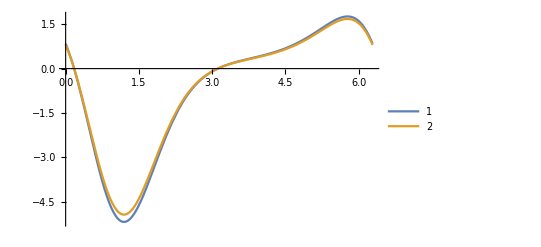

```mathematica
myt2=Pi/4;
bJ=1.0;
bmu=1.0;
nmax=5
Plot[{pvx10[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]]*1.05,pvx20[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
```

4.18632

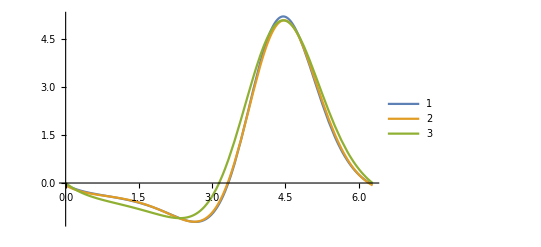

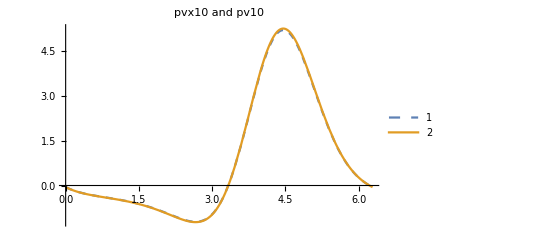

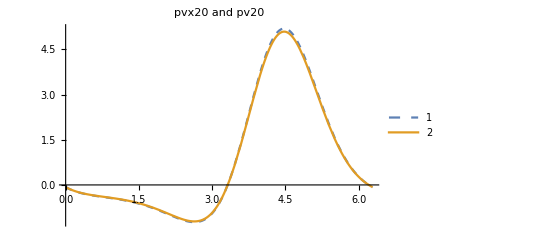

```mathematica
myt2=RandomReal[{0,2Pi}]
bJ=1.0;
bmu=1.0;
nmax=2;
jmax=10;
Plot[{pvx10[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]],pvx20[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]],pv10[1.0,1.0,theta2,myt2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
Plot[{pvx10[ theta1,myt2,nmax]Exp[Cos[theta1-myt2]],pv10[1.0,1.0,theta1,myt2]Exp[Cos[theta1-myt2]]*1.01},{theta1,0,2Pi},PlotStyle->{Dashed,Thick},PlotLegends->Automatic,PlotLabel->"pvx10 and pv10"]
Plot[{pvx20[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]]*1.02,pv20[1.0,1.0,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick},PlotLegends->Automatic,PlotLabel->"pvx20 and pv20"]
```

## test for first order

### Import first order

#### H1ns

```mathematica
H1x=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/H1x.xls"],1];
```

```mathematica
(*c2=RandomInteger[{5,10}];H1[0,c2,theta1]-ToExpression[H1x[[c2+1,2]]]//Simplify*)
```

```mathematica
Table[H1[0,j_,xi_]:=ToExpression[H1x[[j+1,2]]]/.theta1->xi,{j,0,10}];
```

```mathematica
H1cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/H1cx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];c2=RandomInteger[{8,10}];
H1c[c1,c2,theta1]-ToExpression[H1cx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[H1c[n_,j_,xi_]:=ToExpression[H1cx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
H1sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/H1sx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];c2=RandomInteger[{8,10}];
H1s[c1,c2,theta1];//Simplify
H1s[c1,c2,theta1]-ToExpression[H1sx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[H1s[n_,j_,xi_]:=ToExpression[H1sx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### I1ns

```mathematica
I1cchx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/I1cchx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{5,10}]
I1cch[c1,c2,theta1]-ToExpression[I1cchx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[I1cch[n_,j_,xi_]:=ToExpression[I1cchx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1schx=Flatten[Import["/home/weisongl/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1sch.xls"],1];
```

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1].

```mathematica
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{5,10}]
I1sch[c1,c2,theta1]-ToExpression[I1schx[[11*(c1-1)+c2+1,3]]]*)
```

```mathematica
Table[I1sch[n_,j_,xi_]:=ToExpression[I1schx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1cshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/I1cshx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{8,10}]
I1csh[c1,c2,theta1]-ToExpression[I1cshx[[11*(c1-1)+c2+1,3]]]*)
```

```mathematica
Table[I1csh[n_,j_,xi_]:=ToExpression[I1cshx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1sshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/I1sshx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{8,10}]
I1ssh[c1,c2,theta1]-ToExpression[I1sshx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[I1ssh[n_,j_,xi_]:=ToExpression[I1sshx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### F1ns

```mathematica
F1sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/F1sx.xls"],1];
Table[F1s[n_,j_]:=ToExpression[F1sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
F1cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/F1cx.xls"],1];
Table[F1c[n_,j_]:=ToExpression[F1cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

#### E1ns

```mathematica
E1sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/E1sx.xls"],1];
Table[E1s[n_,j_]:=ToExpression[E1sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E1cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/E1cx.xls"],1];
Table[E1c[n_,j_]:=ToExpression[E1cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

#### Ans

```mathematica
A1cx0=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/A1cx0.xls"],1];
Table[A1c[0,j_,theta1_]:=ToExpression[A1cx0[[j+1,2]]],{j,0,10}];
```

```mathematica
A1cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/A1cx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
A1c[c1,c2,theta1]-ToExpression[A1cx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[A1c[n_,j_,theta1_]:=ToExpression[A1cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
A1sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/A1sx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{0,5}];
A1s[c1,c2,theta1]-ToExpression[A1sx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[A1s[n_,j_,theta1_]:=ToExpression[A1sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA1cx0=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/dA1cx0.xls"],1];
Table[dA1c[0,j_,theta1_]:=ToExpression[dA1cx0[[j+1,2]]],{j,0,10}];
```

```mathematica
dA1cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import/dA1cx.xls"],1];
```

```mathematica
Table[dA1c[n_,j_,theta1_]:=ToExpression[dA1cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA1sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/import excels/dA1sx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
dA1s[c1,c2,theta1]-ToExpression[dA1sx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[dA1s[n_,j_,theta1_]:=ToExpression[dA1sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
dA1s[0,j_,theta1_]:=0
```

### A1ns and dA1ns from summing j

```mathematica
Axc1[0,theta1_]:=-1/4 bmu^2 (BesselI[0,bJ]+2 BesselI[1,bJ]+BesselI[2,bJ]) Sin[theta1]^2
```

```mathematica
Axc1[n_,theta1_]:=1/(4 n^2)bmu^2 (1/(2+(-2+n) n)n^2 BesselI[-2+n,bJ] (Cos[(-2+n) theta1]-Cosh[n theta1])+1/(bJ^2 (4+n^4) BesselI[0,bJ])(-4 bJ (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Cos[n theta1]+2 n^2 (2+(-2+n) n) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Cos[(2+n) theta1]+bJ n^2 (2+n (2+n)) BesselI[0,bJ] (bJ BesselI[n,bJ] (Cos[(-2+n) theta1]+Cosh[n theta1])+2 BesselI[-1+n,bJ] (bJ Cos[(-2+n) theta1]+(-1+n) Cosh[n theta1]))))
```

```mathematica
dAxc1[n_,theta1_]:=1/4 bmu^2 (-((-2+n) BesselI[-2+n,bJ] Sin[(-2+n) theta1])/(2+(-2+n) n)+1/(bJ^2 n (4+n^4) BesselI[0,bJ])(bJ (-bJ n (-4-2 n+n^3) BesselI[0,bJ] (2 BesselI[-1+n,bJ]+BesselI[n,bJ]) Sin[(-2+n) theta1]+4 (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Sin[n theta1])-2 n (4-2 n+n^3) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Sin[(2+n) theta1]))
```

```mathematica
D[Axc1[n,theta1],theta1]-dAxc1[n,theta1]//FullSimplify
```

1/(4.+n^4)n ((2.+n (2.+1. n)) (-0.25 BesselI[-2+n,1.]+(-0.5+0.5 n) BesselI[-1+n,1.])+(0.5+(0.5+0.25 n) n) BesselI[n,1.]) Sinh[n theta1]

```mathematica
dAxc1[0,theta1_]:=-1/4 bmu^2 (BesselI[0,bJ]+2 BesselI[1,bJ]+BesselI[2,bJ]) Sin[2 theta1]
```

```mathematica
Axs1[n_,theta1_]:=1/(4 n^2)bmu^2 ((n^2 BesselI[-2+n,bJ] Sin[(-2+n) theta1])/(2+(-2+n) n)+1/(bJ^2 (4+n^4) BesselI[0,bJ])(bJ (bJ n^2 (2+n (2+n)) BesselI[0,bJ] (2 BesselI[-1+n,bJ]+BesselI[n,bJ]) Sin[(-2+n) theta1]-4 (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Sin[n theta1])+2 n^2 (2+(-2+n) n) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Sin[(2+n) theta1]))
```

```mathematica
dAxs1[n_,theta1_]:=1/4 bmu^2 (((-2+n) BesselI[-2+n,bJ] Cos[(-2+n) theta1])/(2+(-2+n) n)+(bJ (bJ n (-4-2 n+n^3) BesselI[0,bJ] (2 BesselI[-1+n,bJ]+BesselI[n,bJ]) Cos[(-2+n) theta1]-4 (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Cos[n theta1])+2 n (4-2 n+n^3) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Cos[(2+n) theta1])/(bJ^2 n (4+n^4) BesselI[0,bJ]))
```

```mathematica
D[Axs1[n,theta1],theta1]-dAxs1[n,theta1]//FullSimplify
```

0.

```mathematica
Axs1[0,theta1_]:=0
dAxs1[0,theta1_]:=0
```

### test for Hns

#### H1

```mathematica
(*Sum[H1[0,j,theta1],{j,0,3}]//Simplify*)
```

1/(16 BesselI[0,bJ])bmu^2 (4 (4+bJ^2) BesselI[1,bJ]-BesselI[0,bJ] (2 bJ (8+bJ^2) Cos[theta1]^2+(8+3 bJ^2) Cos[2 theta1]))

-1/2 (BesselI[0,2]+2 BesselI[1,2]+BesselI[2,2]) Cos[2 theta1]

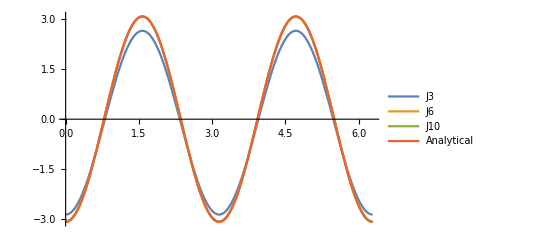

```mathematica
(*bmu=1;bJ=2;
t13=Sum[H1[0,j,theta1],{j,0,3}];
t16=Sum[H1[0,j,theta1],{j,0,6}];
t110=Sum[H1[0,j,theta1],{j,0,10}];
t2=-1/2 bmu^2 (BesselI[0,bJ]+2 BesselI[1,bJ]+BesselI[2,bJ]) Cos[2 theta1]
Plot[{t13,t16,t110,t2},{theta1,0,2Pi},PlotLegends->{"J3","J6","J10","Analytical"}]*)
```

#### H1c

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

bmu = 5.27404 ,bJ= 4.08884

```mathematica
bmu=bJ=1
```

```mathematica
(*analytical=-((bmu^2 (-4 BesselI[1,bJ] BesselI[n,bJ] Cos[n theta1]+BesselI[0,bJ] (BesselI[-2+n,bJ] Cos[(-2+n) theta1]+2 BesselI[n,bJ] Cos[2 theta1] Cos[n theta1]+4 Cos[theta1] (BesselI[-1+n,bJ] Cos[(-1+n) theta1]+BesselI[1+n,bJ] Cos[(1+n) theta1])+BesselI[2+n,bJ] Cos[(2+n) theta1])))/(2 BesselI[0,bJ]));*)
```

-1.13952 (-447.734 Cos[theta1]+12.2049 (10.5799 Cos[theta1]+21.1597 Cos[theta1] Cos[2 theta1]+4 Cos[theta1] (12.2049+7.02991 Cos[2 theta1])+3.7027 Cos[3 theta1]))

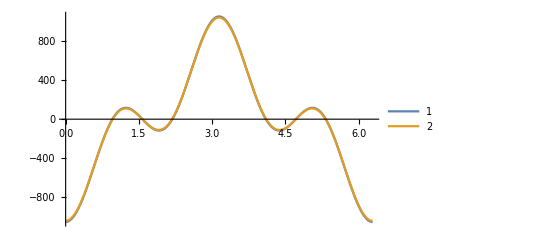

```mathematica
(*aplot=analytical/.{n->1}
series=Sum[H1c[1,j,theta1],{j,0,8}];
Plot[{aplot,series},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

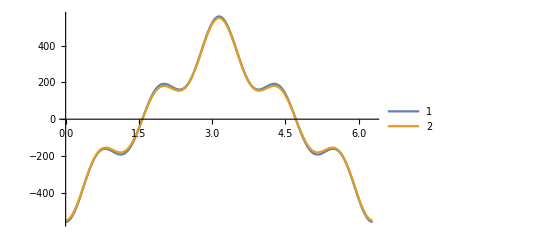

```mathematica
(*aplot=analytical/.{n->3};
series=Sum[H1c[3,j,theta1],{j,0,8}];
Plot[{aplot,series},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

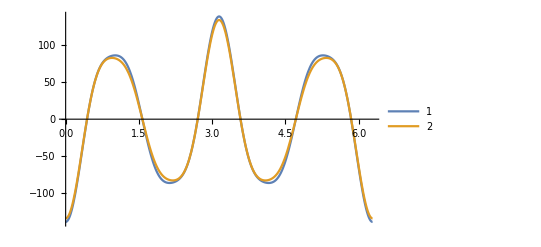

```mathematica
(*aplot=analytical/.{n->5};
series=Sum[H1c[5,j,theta1],{j,0,8}];
Plot[{aplot,series},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

#### H1s

```mathematica
(**)
```

```mathematica
(*analytical=-1/(2 BesselI[0,bJ])bmu^2 (-4 BesselI[1,bJ] BesselI[n,bJ] Sin[n theta1]+BesselI[0,bJ] (BesselI[-2+n,bJ] Sin[(-2+n) theta1]+2 BesselI[n,bJ] Cos[2 theta1] Sin[n theta1]+4 Cos[theta1] (BesselI[-1+n,bJ] Sin[(-1+n) theta1]+BesselI[1+n,bJ] Sin[(1+n) theta1])+BesselI[2+n,bJ] Sin[(2+n) theta1]));*)
```

```mathematica
(*bmu=bJ=1*)
```

1

-1/(2 BesselI[0,1])(-4 BesselI[1,1]^2 Sin[theta1]+BesselI[0,1] (-BesselI[1,1] Sin[theta1]+2 BesselI[1,1] Cos[2 theta1] Sin[theta1]+4 BesselI[2,1] Cos[theta1] Sin[2 theta1]+BesselI[3,1] Sin[3 theta1]))

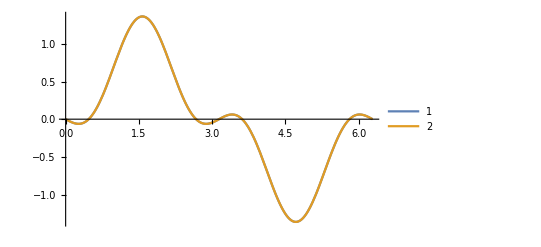

```mathematica
(*aplot=analytical/.{n->1}
series=Sum[H1s[1,j,theta1],{j,0,10}];
Plot[{aplot,series},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

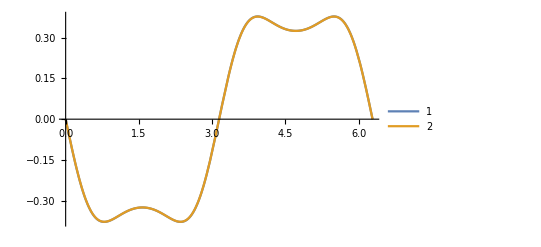

```mathematica
(*aplot=analytical/.{n->3};
series=Sum[H1s[3,j,theta1],{j,0,5}];
Plot[{aplot,series},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

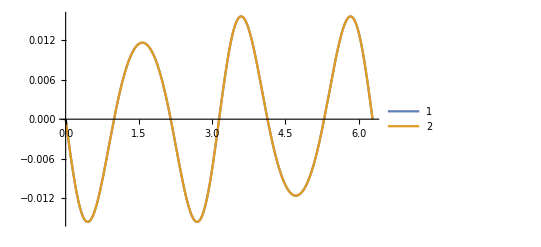

```mathematica
(*aplot=analytical/.{n->5};
series=Sum[H1s[5,j,theta1],{j,0,8}];
Plot[{aplot,series},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

### test for A1ns

#### A1 and dA1

bmu = 8.79432 ,bJ= 5.54559

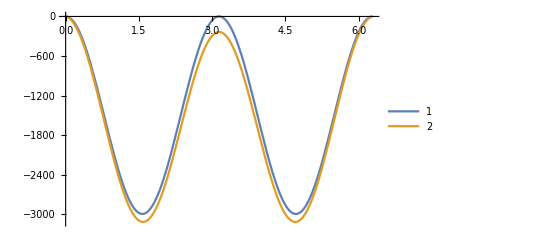

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{1,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
Ax1=-1/4 bmu^2 (BesselI[0,bJ]+2 BesselI[1,bJ]+BesselI[2,bJ]) Sin[theta1]^2;
Ax1Sum=Sum[A1c[0,j,theta1],{j,0,10}];
Plot[{Ax1,Ax1Sum},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

bmu = 3.90078 ,bJ= 7.81323

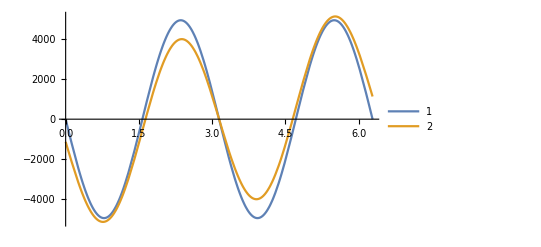

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{1,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
dAx1=-1/4 bmu^2 (BesselI[0,bJ]+2 BesselI[1,bJ]+BesselI[2,bJ]) Sin[2 theta1];
dAx1Sum=Sum[dA1c[0,j,theta1],{j,0,10}];
Plot[{dAx1,dAx1Sum},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

### test for Axcn and dAxcn

2.4228

5.78043

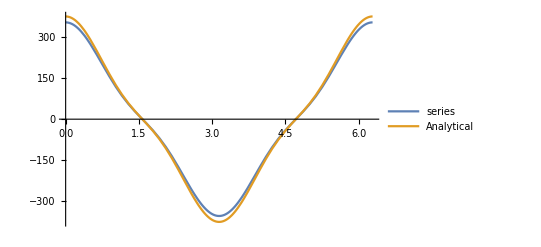

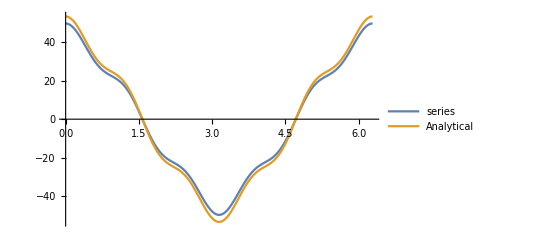

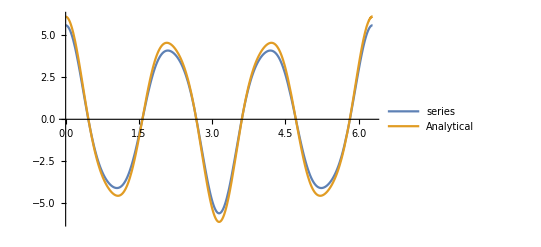

```mathematica
(*bmu=RandomReal[{0.001,10}]
bJ=RandomReal[{0.001,10}]
A1cxn[n_]:=1/(4 n^2)bmu^2 ((n^2 BesselI[-2+n,bJ] (Cos[(-2+n) theta1]-Cosh[n theta1]))/(2+(-2+n) n)+1/(bJ^2 (4+n^4) BesselI[0,bJ])(-4 bJ (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Cos[n theta1]+2 n^2 (2+(-2+n) n) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Cos[(2+n) theta1]+bJ n^2 (2+n (2+n)) BesselI[0,bJ] (bJ BesselI[n,bJ] (Cos[(-2+n) theta1]+Cosh[n theta1])+2 BesselI[-1+n,bJ] (bJ Cos[(-2+n) theta1]+(-1+n) Cosh[n theta1]))))
Plot[{Sum[A1c[1,j,theta1],{j,0,10}],A1cxn[1]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A1c[3,j,theta1],{j,0,10}],A1cxn[3]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A1c[5,j,theta1],{j,0,10}],A1cxn[5]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]*)
```

7.25715

4.67985

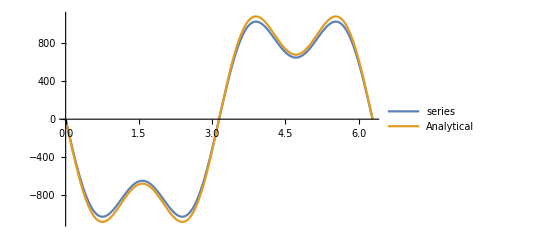

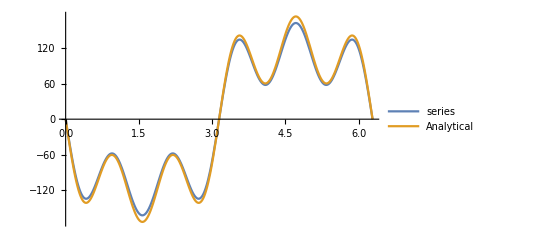

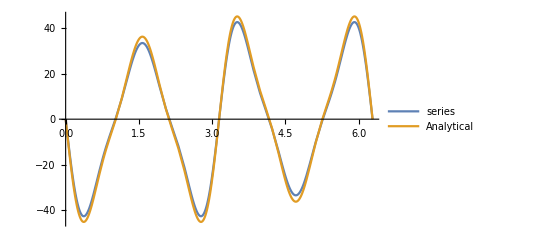

```mathematica
(*bmu=RandomReal[{0.001,10}]
bJ=RandomReal[{0.001,10}]
dA1cxn[n_]:=1/4 bmu^2 (-((-2+n) BesselI[-2+n,bJ] Sin[(-2+n) theta1])/(2+(-2+n) n)+1/(bJ^2 n (4+n^4) BesselI[0,bJ])(bJ (-bJ n (-4-2 n+n^3) BesselI[0,bJ] (2 BesselI[-1+n,bJ]+BesselI[n,bJ]) Sin[(-2+n) theta1]+4 (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Sin[n theta1])-2 n (4-2 n+n^3) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Sin[(2+n) theta1]));
Plot[{Sum[dA1c[1,j,theta1],{j,0,10}],dA1cxn[1]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[dA1c[3,j,theta1],{j,0,10}],dA1cxn[3]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[dA1c[5,j,theta1],{j,0,10}],dA1cxn[5]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]*)
```

#### Axsn

0.652695

0.353252

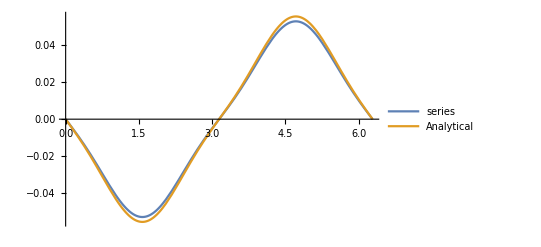

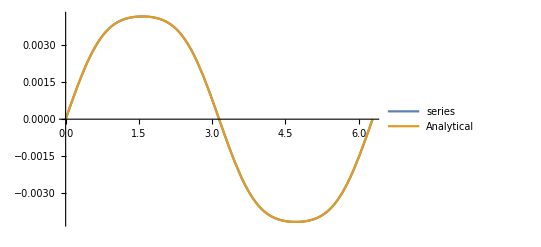

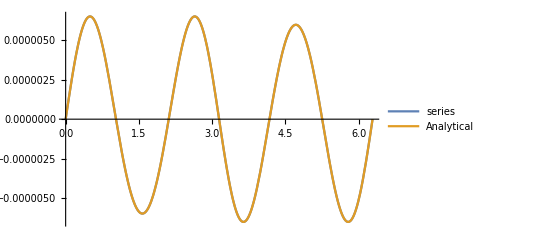

```mathematica
(*A1sxn[n_,theta1_]:=1/(4 n^2)bmu^2 ((n^2 BesselI[-2+n,bJ] Sin[(-2+n) theta1])/(2+(-2+n) n)+1/(bJ^2 (4+n^4) BesselI[0,bJ])(bJ (bJ n^2 (2+n (2+n)) BesselI[0,bJ] (2 BesselI[-1+n,bJ]+BesselI[n,bJ]) Sin[(-2+n) theta1]-4 (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Sin[n theta1])+2 n^2 (2+(-2+n) n) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Sin[(2+n) theta1]))
bmu=RandomReal[{0.001,10}]
bJ=RandomReal[{0.001,10}]
Plot[{Sum[A1s[1,j,theta1],{j,0,10}],A1sxn[1,theta1]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A1s[3,j,theta1],{j,0,10}],A1sxn[3,theta1]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A1s[5,j,theta1],{j,0,10}],A1sxn[5,theta1]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]*)
```

### pvns

```mathematica
pv11[bJx_,bmux_,xi_,xj_]:=Release[Sum[dA1s[n,j,theta1]Sin[n theta2]+dA1c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,nmax},{j,0,jmax}]]
pv21[bJx_,bmux_,xi_,xj_]:=Release[Sum[n A1s[n,j,theta1]Cos[n theta2]-n A1c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,1,nmax},{j,0,jmax}]]
```

```mathematica
pvx11[theta1_,theta2_,nmax_]:=Sum[dAxs1[n,theta1]Sin[n theta2]+dAxc1[n,theta1]Cos[n theta2],{n,0,nmax}]
pvx21[theta1_,theta2_,nmax_]:=Sum[n Axs1[n,theta1]Cos[n theta2]-n Axc1[n,theta1]Sin[n theta2],{n,1,nmax}]
pvx11n[theta1_,theta2_,n_]:=dAxs1[n,theta1]Sin[n theta2]+dAxc1[n,theta1]Cos[n theta2]
pvx21n[theta1_,theta2_,n_]:=n Axs1[n,theta1]Cos[n theta2]-n Axc1[n,theta1]Sin[n theta2]
```

```mathematica
nmax=1
jmax=10;
```

1

0.0170525

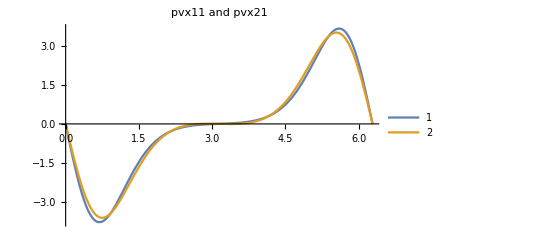

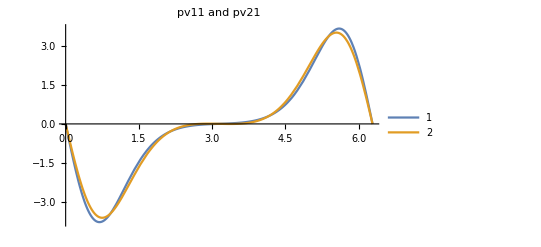

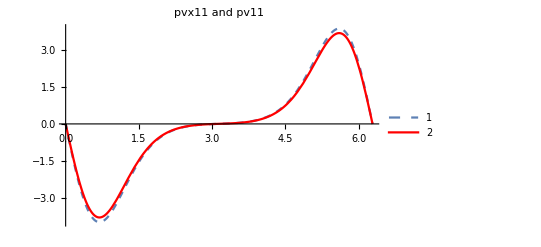

```mathematica
myt2=RandomReal[{0,2Pi}]
bJ=1.0;
bmu=1.0;
nmax=2;
jmax=10;
Plot[{pvx11[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]],pvx21[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic,PlotLabel->"pvx11 and pvx21"]
Plot[{pv11[1.0,1.0,theta2,myt2]Exp[Cos[theta2-myt2]],pv21[1.0,1.0,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic,PlotLabel->"pv11 and pv21"]
Plot[{pvx11[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]]*1.05,pv11[1.0,1.0,theta2,myt2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic,PlotLabel->"pvx11 and pv11",PlotStyle->{Dashed,Red}]
```

Note That I test for pvn for x direction,it passed

y direction

## zero order

### Expressions set up

#### vE

```mathematica
Qy0=0;
Qy1=bmu^2+(bmu^2 BesselI[1,bJ])/BesselI[0,bJ];
F0[j_,theta1_,theta2_]:=(bJ)^j/j! Cos[theta1-theta2]^j (Qy0-bmu(Sin[theta1]+Sin[theta2]))
F1[j_,theta1_,theta2_]:=(bJ)^j/j!Cos[theta1-theta2]^j(Qy1-bmu^2(Sin[theta1]+Sin[theta2])^2+Qy0 bmu(Sin[theta1]+Sin[theta2]))
```

```mathematica
H0[0,j_,theta1_]:=1/(2Pi)Integrate[F0[j,theta1,theta2],{theta2,0,2Pi}]
H0c[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H0s[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
```

```mathematica
I0cch[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0csh[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I0sch[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0ssh[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
```

```mathematica
F0s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0sch[n,j,2Pi]+1/(2n)I0ssh[n,j,2Pi]
F0c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0cch[n,j,2Pi]+1/(2n)I0csh[n,j,2Pi]
```

```mathematica
E0s[n_,j_]:=F0s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0ssh[n,j,2Pi]
E0c[n_,j_]:=F0c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0csh[n,j,2Pi]
```

```mathematica
A0c[0,j_,theta1_]:=Integrate[H0[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A0s[0,j_,theta1_]:=0
A0s[n_,j_,theta1_]:=E0s[n,j]Sinh[n theta1]+F0s[n,j]Cosh[n theta1]+1/n I0ssh[n,j,theta1]
A0c[n_,j_,theta1_]:=E0c[n,j]Sinh[n theta1]+F0c[n,j]Cosh[n theta1]+1/n I0csh[n,j,theta1]
```

```mathematica
dA0c[0,j_,theta1_]:=Integrate[H0[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA0s[0,j_,theta1_]:=0
dA0s[n_,j_,theta1_]:=n E0s[n,j]Cosh[n theta1]+n F0s[n,j]Sinh[n theta1]+I0sch[n,j,theta1]
dA0c[n_,j_,theta1_]:=n E0c[n,j]Cosh[n theta1]+n F0c[n,j]Sinh[n theta1]+I0cch[n,j,theta1]
```

```mathematica
pv10[bJx_,bmux_,xi_,xj_]:=Sum[dA0s[n,j,theta1]Sin[n theta2]+dA0c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,nmax},{j,0,jmax}]
pv20[bJx_,bmux_,xi_,xj_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,1,nmax},{j,0,jmax}]
```

### Import

#### hns

Hns

```mathematica
H0y=Flatten[Import["~/Dropbox/Export/Y/H0y.xls"],1];
Table[H0[0,j_,xi_]:=ToExpression[H0y[[j+1,2]]]/.theta1->xi,{j,0,10}];
```

```mathematica
H0cy=Flatten[Import["~/Dropbox/Export/Y/H0cy.xls"],1];
Table[H0c[n_,j_,xi_]:=ToExpression[H0cy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
H0sy=Flatten[Import["~/Dropbox/Export/Y/H0sy.xls"],1];
Table[H0s[n_,j_,xi_]:=ToExpression[H0sy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

Ins

#### Ins

```mathematica
I0cchy=Flatten[Import["~/Dropbox/Export/Y/I0cchy.xls"],1];
Table[I0cch[n_,j_,xi_]:=ToExpression[I0cchy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0schy=Flatten[Import["~/Dropbox/Export/Y/I0schy.xls"],1];
Table[I0sch[n_,j_,xi_]:=ToExpression[I0schy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0cshy=Flatten[Import["~/Dropbox/Export/Y/I0cshy.xls"],1];
Table[I0csh[n_,j_,xi_]:=ToExpression[I0cshy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0sshy=Flatten[Import["~/Dropbox/Export/Y/I0sshy.xls"],1];
Table[I0ssh[n_,j_,xi_]:=ToExpression[I0sshy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### Fns and Ens

```mathematica
F0sy=Flatten[Import["~/Dropbox/Export/Y/F0sy.xls"],1];
Table[F0s[n_,j_]:=ToExpression[F0sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
F0cy=Flatten[Import["~/Dropbox/Export/Y/F0cy.xls"],1];
Table[F0c[n_,j_]:=ToExpression[F0cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E0sy=Flatten[Import["~/Dropbox/Export/Y/E0sy.xls"],1];
Table[E0s[n_,j_]:=ToExpression[E0sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E0cy=Flatten[Import["~/Dropbox/Export/Y/E0cy.xls"],1];
Table[E0c[n_,j_]:=ToExpression[E0cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

#### Ans

```mathematica
A0cy0=Flatten[Import["~/Dropbox/Export/Y/A0cy0.xls"],1];
A0cy=Flatten[Import["~/Dropbox/Export/Y/A0cy.xls"],1];
Table[A0c[0,j_,theta1_]:=ToExpression[A0cy0[[j+1,2]]],{j,0,10}];  
Table[A0c[n_,j_,theta1_]:=ToExpression[A0cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
A0sy=Flatten[Import["~/Dropbox/Export/Y/A0sy.xls"],1];
A0s[0,j,theta1]:=0;
Table[A0s[n_,j_,theta1_]:=ToExpression[A0sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA0cy0=Flatten[Import["~/Dropbox/Export/Y/dA0cy0.xls"],1];
dA0cy=Flatten[Import["~/Dropbox/Export/Y/dA0cy.xls"],1];
Table[dA0c[0,j_,theta1_]:=ToExpression[dA0cy0[[j+1,2]]],{j,0,10}];
Table[dA0c[n_,j_,theta1_]:=ToExpression[dA0cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA0sy=Flatten[Import["~/Dropbox/Export/Y/dA0sy.xls"],1];
dA0s[0,j,theta1]:=0;
Table[dA0s[n_,j_,theta1_]:=ToExpression[dA0sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

### A0ns and dA0ns summing j

```mathematica
Ayc0[n_,theta1_]:=1/(bJ+4 bJ n^4)(2 bmu ((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ]) Cos[n theta1] Sin[theta1]-2 bmu n (2 bJ BesselI[-1+n,bJ]+(1+2 bJ+2 (-1+n) n) BesselI[n,bJ]) Cos[theta1] Sin[n theta1])
Ayc0[0,theta1_]:=bmu (BesselI[0,bJ]+BesselI[1,bJ]) Sin[theta1]
```

```mathematica
dAyc0[n_,theta1_]:=1/(bJ+4 bJ n^4)2 bmu ((bJ BesselI[-1+n,bJ]+(bJ+n (-1+n-2 n^3)) BesselI[n,bJ]) Cos[theta1] Cos[n theta1]+n (BesselI[n,bJ]+(-1+2 n^2) (-bJ BesselI[-1+n,bJ]+(-bJ+n) BesselI[n,bJ])) Sin[theta1] Sin[n theta1])
dAyc0[0,theta1_]:=bmu (BesselI[0,bJ]+BesselI[1,bJ]) Cos[theta1]
```

```mathematica
Ays0[n_,theta1_]:=1/(bJ+4 bJ n^4)bmu (bJ (1+2 (-1+n) n) BesselI[1+n,bJ] (-Cos[theta1+n theta1]+Cosh[n theta1])+bJ BesselI[-1+n,bJ] ((1+2 n (1+n)) Cos[(-1+n) theta1]+(-1-2 (-1+n) n) Cosh[n theta1])+2 BesselI[n,bJ] (2 bJ n Cos[theta1] Cos[n theta1]+n (1+2 (-1+n) n) Cosh[n theta1]+bJ (1+2 n^2) Sin[theta1] Sin[n theta1]))
Ays0[0,theta1_]:=0
```

```mathematica
dAys0[n_,theta1_]:=1/(1+4 n^4)bmu ((1+n-2 n^3) BesselI[-1+n,bJ] Sin[(-1+n) theta1]+2 BesselI[n,bJ] (n (-1+2 n^2) Cos[n theta1] Sin[theta1]+Cos[theta1] Sin[n theta1])+(1-n+2 n^3) BesselI[1+n,bJ] Sin[theta1+n theta1])
dAys0[0,theta1_]:=0
```

### test for Hns

#### H0

```mathematica
(*H0nNumerical[bJ_,bmu_,theta1_]:=NIntegrate[Exp[bJ Cos[theta1-theta2]] (0-bmu(Sin[theta1]+Sin[theta2])),{theta2,0,2Pi}]/2/Pi*)
```

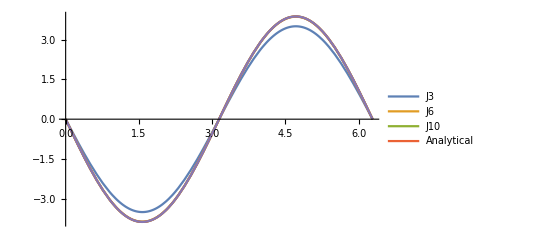

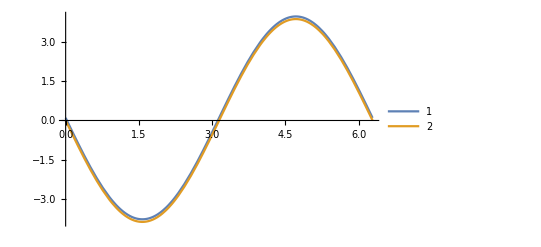

```mathematica
(*bmu=1;bJ=2;
t13=Sum[H0[0,j,theta1],{j,0,3}];
t16=Sum[H0[0,j,theta1],{j,0,6}];
t110=Sum[H0[0,j,theta1],{j,0,10}];
analytical=-bmu (BesselI[0,bJ]+BesselI[1,bJ]) Sin[theta1];
Plot[{t13,t16,t110,analytical,H0nNumerical[bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->{"J3","J6","J10","Analytical"}]
Plot[{analytical*1.05,H0nNumerical[bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->{"1","2"}]*)
```

```mathematica
(**)
```

#### H0c

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

bmu = 8.46083 ,bJ= 6.92378

```mathematica
(*HncNumerical[n_,bJ_,bmu_,theta1_]:=NIntegrate[Cos[n theta2]Exp[bJ Cos[theta1-theta2]] (0-bmu(Sin[theta1]+Sin[theta2])),{theta2,0,2Pi}]/Pi
a[n_]:=-bmu (2 BesselI[n,bJ] Cos[n theta1] Sin[theta1]-BesselI[-1+n,bJ] Sin[(-1+n) theta1]+BesselI[1+n,bJ] Sin[(1+n) theta1])*)
```

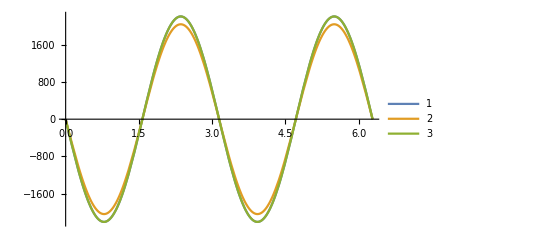

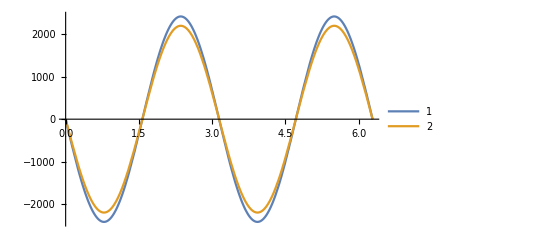

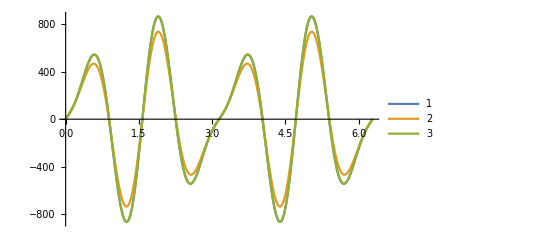

```mathematica
(*series[n_]:=Sum[H0c[n,j,theta1],{j,0,10}]
Plot[{a[1],series[1],HncNumerical[1,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{a[1]*1.1,HncNumerical[1,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{a[5],series[5],HncNumerical[5,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

#### H0s

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

bmu = 0.825604 ,bJ= 1.3248

```mathematica
(*HnsNumerical[n_,bJ_,bmu_,theta1_]:=NIntegrate[Sin[n theta2]Exp[bJ Cos[theta1-theta2]] (0-bmu(Sin[theta1]+Sin[theta2])),{theta2,0,2Pi}]/Pi*)
```

```mathematica
(*a[n_]:=-bmu (BesselI[-1+n,bJ] Cos[(-1+n) theta1]-BesselI[1+n,bJ] Cos[(1+n) theta1]+2 BesselI[n,bJ] Sin[theta1] Sin[n theta1])
series[n_]:=Sum[H0s[n,j,theta1],{j,0,10}];*)
```

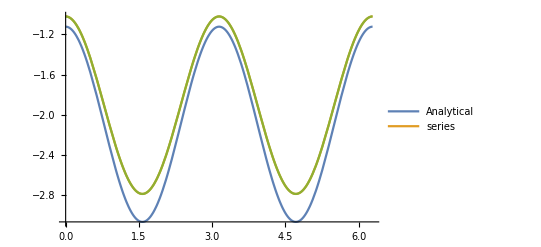

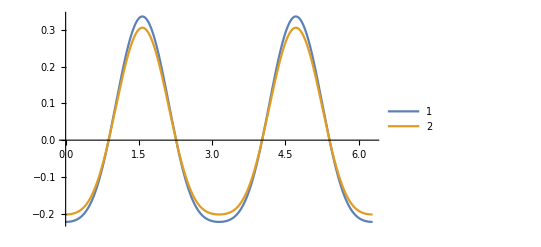

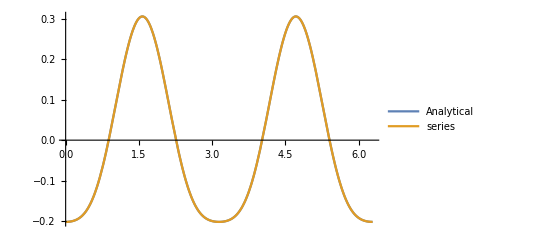

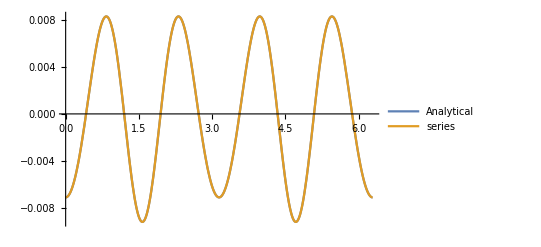

```mathematica
(*
Plot[{a[1]*1.1,series[1],HnsNumerical[1,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->{"Analytical","series"}]
Plot[{a[3]*1.1,HnsNumerical[3,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{a[3],series[3]},{theta1,0,2Pi},PlotLegends->{"Analytical","series"}]
Plot[{a[5],series[5]},{theta1,0,2Pi},PlotLegends->{"Analytical","series"}]
*)
```

```mathematica
(**)
```

### test for F0ns and E0ns

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

bmu = 5.39774 ,bJ= 7.28836

```mathematica
(*F0cn[n_]:=1/n^2 bmu (BesselI[1+n,bJ] Sin[(1+n) theta1]+BesselI[-1+n,bJ] Sin[theta1-n theta1]);*)
```

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];*)
```

value start to change for bJ get biggers

```mathematica
(*E0sn[n_]:=1/(bJ+4 bJ n^4)2 bmu (-BesselI[n,bJ]+(-1+2 n^2) (bJ BesselI[-1+n,bJ]+(bJ-n) BesselI[n,bJ]))*)
```

does not agree!!

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
Sum[E0s[1,j],{j,0,10}]//N
E0sn[1]//N
Sum[E0s[3,j],{j,0,10}]//N
E0sn[3]//N
Sum[E0s[5,j],{j,0,10}]//N
E0sn[5]//N*)
```

bmu = 8.03967 ,bJ= 4.98876

0.

133.128

0.

17.8808

0.

1.58302

```mathematica
(*Table[E0c[n,j],{n,1,5},{j,0,10}]*)
```

{{0.,8.02159,10.0044,24.9548,20.7489,25.8779,16.1373,13.4175,6.69366,4.17413,1.73531},{0.,-2.0054,0.384786,-3.83921,0.798036,-2.73708,0.620665,-1.03212,0.257449,-0.240815,0.0667427},{0.,0.,-1.28262,0.0426579,-1.96849,0.0663535,-1.20823,0.0412846,-0.411918,0.0142705,-0.0902616},{0.,0.,0.,-0.623871,0.0063259,-0.77318,0.00787185,-0.399252,0.0040815,-0.117807,0.00120928},{0.,0.,0.,0.,-0.253036,0.0010347,-0.261965,0.00107297,-0.116232,0.000476853,-0.0300832}}

### test for A0ns

#### A0 and dA0

4

bmu = 8.81937 ,bJ= 4

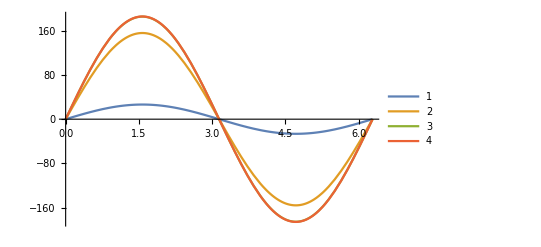

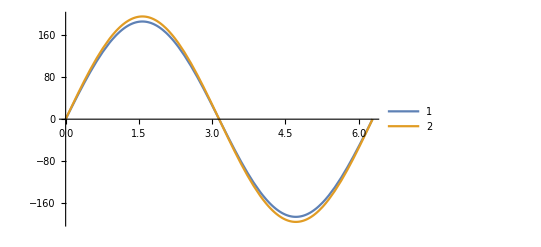

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
bJ=4
Print["bmu = ",bmu," ,bJ= " , bJ]
A0=bmu (BesselI[0,bJ]+BesselI[1,bJ]) Sin[theta1];
s1=Sum[A0c[0,j,theta1],{j,0,1}];
s5=Sum[A0c[0,j,theta1],{j,0,5}];
s10=Sum[A0c[0,j,theta1],{j,0,10}];
Plot[{s1,s5,s10,A0},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s10,A0*1.05},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

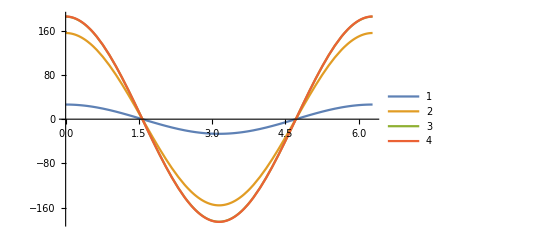

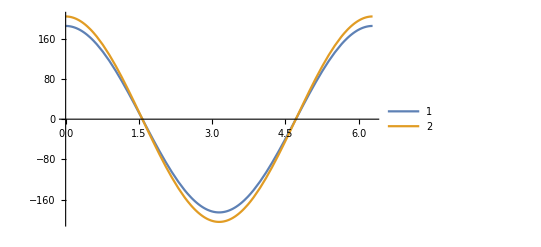

```mathematica
(*dA0=bmu (BesselI[0,bJ]+BesselI[1,bJ]) Cos[theta1];
s1=Sum[dA0c[0,j,theta1],{j,0,1}];
s5=Sum[dA0c[0,j,theta1],{j,0,5}];
s10=Sum[dA0c[0,j,theta1],{j,0,10}];
Plot[{s1,s5,s10,dA0},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s10,dA0*1.1},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

#### Acyn and dAcyn

bmu = 4.50623 ,bJ= 2.84058

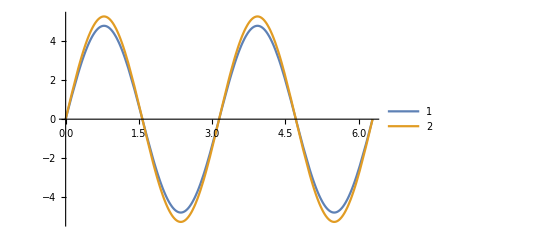

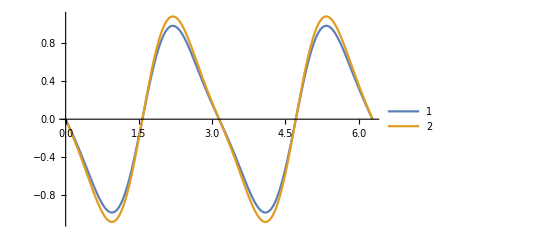

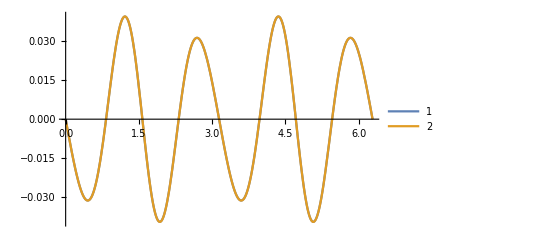

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
Acyn[n_]:=1/(bJ+4 bJ n^4)(2 bmu ((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ]) Cos[n theta1] Sin[theta1]-2 bmu n (2 bJ BesselI[-1+n,bJ]+(1+2 bJ+2 (-1+n) n) BesselI[n,bJ]) Cos[theta1] Sin[n theta1])
s1=Sum[A0c[1,j,theta1],{j,0,10}];
s3=Sum[A0c[3,j,theta1],{j,0,10}];
s5=Sum[A0c[5,j,theta1],{j,0,10}];
Plot[{s1,Acyn[1]*1.1},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s3,Acyn[3]*1.1},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s5,Acyn[5]},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

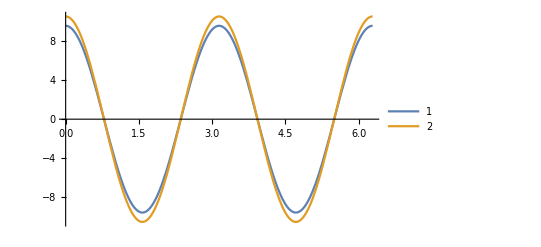

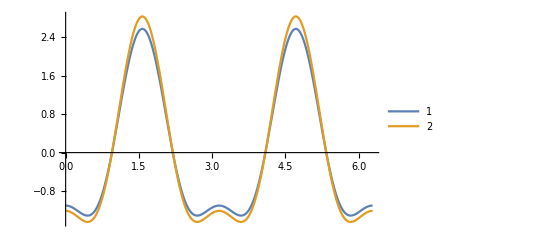

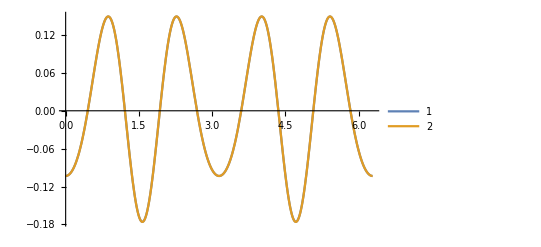

```mathematica
(*dAcyn[n_]:=1/(bJ+4 bJ n^4)2 bmu ((bJ BesselI[-1+n,bJ]+(bJ+n (-1+n-2 n^3)) BesselI[n,bJ]) Cos[theta1] Cos[n theta1]+n (BesselI[n,bJ]+(-1+2 n^2) (-bJ BesselI[-1+n,bJ]+(-bJ+n) BesselI[n,bJ])) Sin[theta1] Sin[n theta1])
s1=Sum[dA0c[1,j,theta1],{j,0,10}];
s3=Sum[dA0c[3,j,theta1],{j,0,10}];
s5=Sum[dA0c[5,j,theta1],{j,0,10}];
Plot[{s1,dAcyn[1]*1.1},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s3,dAcyn[3]*1.1},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s5,dAcyn[5]},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

#### Asyn and dAsyn

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

bmu = 6.67141 ,bJ= 2.54098

bmu = 7.76812 ,bJ= 9.96445

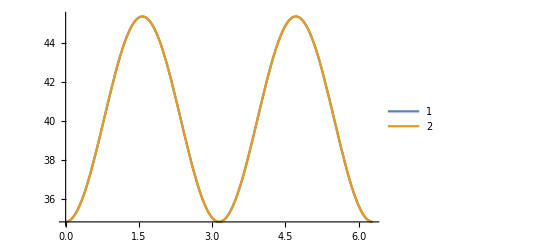

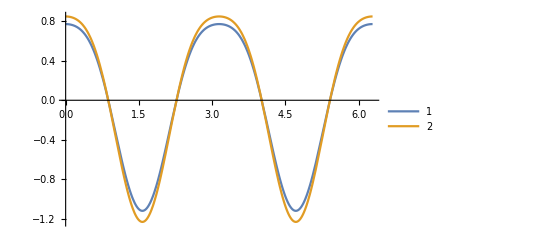

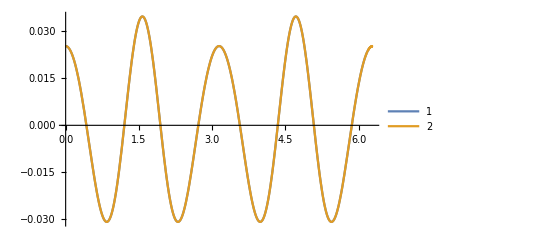

```mathematica
(*Asyn[n_]:=1/(bJ+4 bJ n^4)bmu (bJ (1+2 (-1+n) n) BesselI[1+n,bJ] (-Cos[theta1+n theta1]+Cosh[n theta1])+bJ BesselI[-1+n,bJ] ((1+2 n (1+n)) Cos[(-1+n) theta1]+(-1-2 (-1+n) n) Cosh[n theta1])+2 BesselI[n,bJ] (2 bJ n Cos[theta1] Cos[n theta1]+n (1+2 (-1+n) n) Cosh[n theta1]+bJ (1+2 n^2) Sin[theta1] Sin[n theta1]))
s1=Sum[A0s[1,j,theta1],{j,0,10}];
s3=Sum[A0s[3,j,theta1],{j,0,10}];
s5=Sum[A0s[5,j,theta1],{j,0,10}];
Plot[{s1,Asyn[1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s3,Asyn[3]*1.1},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s5,Asyn[5]},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

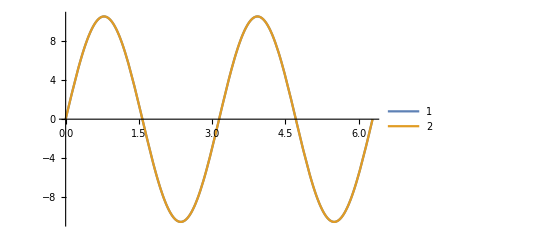

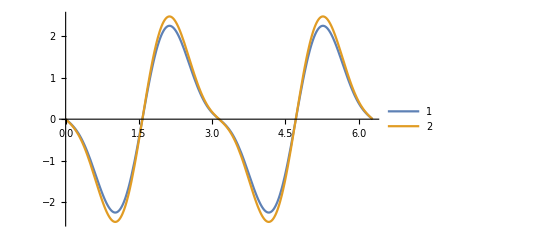

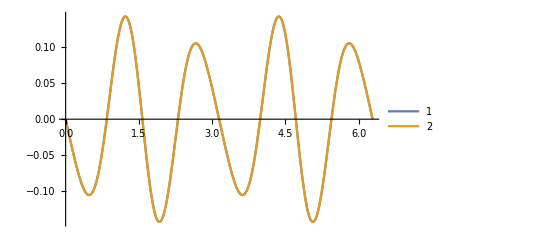

```mathematica
(*dAsyn[n_]:=1/(1+4 n^4)bmu ((1+n-2 n^3) BesselI[-1+n,bJ] Sin[(-1+n) theta1]+2 BesselI[n,bJ] (n (-1+2 n^2) Cos[n theta1] Sin[theta1]+Cos[theta1] Sin[n theta1])+(1-n+2 n^3) BesselI[1+n,bJ] Sin[theta1+n theta1])
s1=Sum[dA0s[1,j,theta1],{j,0,10}];
s3=Sum[dA0s[3,j,theta1],{j,0,10}];
s5=Sum[dA0s[5,j,theta1],{j,0,10}];
Plot[{s1,dAsyn[1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s3,dAsyn[3]*1.1},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s5,dAsyn[5]},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

### test for pv0ns

```mathematica
pvy10[theta1_,theta2_,nmax_]:=Sum[dAys0[n,theta1]Sin[n theta2]+dAyc0[n,theta1]Cos[n theta2],{n,0,nmax}]
pvy20[theta1_,theta2_,nmax_]:=Sum[n Ays0[n,theta1]Cos[n theta2]-n Ayc0[n,theta1]Sin[n theta2],{n,1,nmax}]
pvy10n[theta1_,theta2_,nmax_]:=dAys0[n,theta1]Sin[n theta2]+dAyc0[n,theta1]Cos[n theta2]
pvy20n[theta1_,theta2_,nmax_]:=n Ays0[n,theta1]Cos[n theta2]-n Ayc0[n,theta1]Sin[n theta2]
```

2

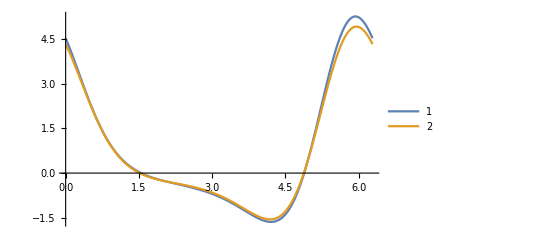

```mathematica
myt2=RandomReal[{0,2Pi}];
bJ=1.0;
bmu=1.0;
nmax=2
Plot[{pvy10[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]]*1.05,pvy20[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
```

2.20592

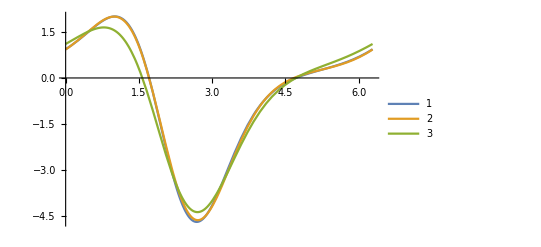

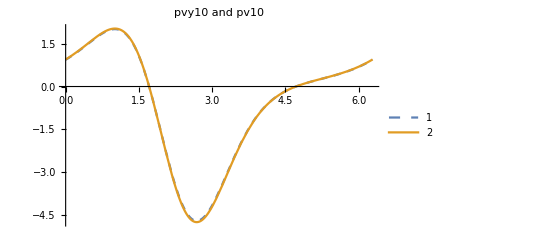

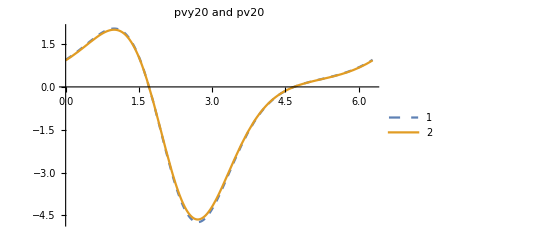

```mathematica
myt2=RandomReal[{0,2Pi}]
bJ=1.0;
bmu=1.0;
nmax=2;
jmax=10;
Plot[{pvy10[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]],pvy20[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]],pv10[1.0,1.0,theta2,myt2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
Plot[{pvy10[ theta1,myt2,nmax]Exp[Cos[theta1-myt2]],pv10[1.0,1.0,theta1,myt2]Exp[Cos[theta1-myt2]]*1.01},{theta1,0,2Pi},PlotStyle->{Dashed,Thick},PlotLegends->Automatic,PlotLabel->"pvy10 and pv10"]
Plot[{pvy20[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]]*1.02,pv20[1.0,1.0,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick},PlotLegends->Automatic,PlotLabel->"pvy20 and pv20"]
```

## First order

### Set up

#### vEE

```mathematica
H1[0,j_,theta1_]:=1/(2Pi)Integrate[F1[j,theta1,theta2],{theta2,0,2Pi}]
H1c[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H1s[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
```

```mathematica
I1cch[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1csh[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I1sch[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1ssh[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
```

small question here, I1CCH integrate along theta1?

```mathematica
F1s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I1sch[n,j,2Pi]+1/(2n)I1ssh[n,j,2Pi]
F1c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I1cch[n,j,2Pi]+1/(2n)I1csh[n,j,2Pi]
E1s[n_,j_]:=F1s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I1ssh[n,j,2Pi]
E1c[n_,j_]:=F1c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I1csh[n,j,2Pi]
```

```mathematica
A1c[0,j_,theta1_]:=Integrate[H1[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H1[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A1s[0,j_,theta1_]:=0
A1s[n_,j_,theta1_]:=E1s[n,j]Sinh[n theta1]+F1s[n,j]Cosh[n theta1]+1/n I1ssh[n,j,theta1]
A1c[n_,j_,theta1_]:=E1c[n,j]Sinh[n theta1]+F1c[n,j]Cosh[n theta1]+1/n I1csh[n,j,theta1]
dA1c[0,j_,theta1_]:=Integrate[H1[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H1[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA1s[0,j_,theta1_]:=0
dA1s[n_,j_,theta1_]:=n E1s[n,j]Cosh[n theta1]+n F1s[n,j]Sinh[n theta1]+I1sch[n,j,theta1]
dA1c[n_,j_,theta1_]:=n E1c[n,j]Cosh[n theta1]+n F1c[n,j]Sinh[n theta1]+I1cch[n,j,theta1]
```

### Import

```mathematica
(*Export["~/Dropbox/Export/Y/H1yMore.xls",Table[{j,H1[0,j,theta1]},{j,0,20}]//Simplify];*)
Timing[%]
```

{0.000011,Null}

```mathematica
(*H1y=Flatten[Import["~/Dropbox/Export/Y/H1yMore.xls"],1];
Table[H1[0,j_,xi_]:=ToExpression[H1y[[j+1,2]]]/.theta1->xi,{j,0,20}];*)
```

```mathematica
H1y=Flatten[Import["~/Dropbox/Export/Y/H1y.xls"],1];
Table[H1[0,j_,xi_]:=ToExpression[H1y[[j+1,2]]]/.theta1->xi,{j,0,10}];
```

```mathematica
H1cy=Flatten[Import["~/Dropbox/Export/Y/H1cy.xls"],1];
```

```mathematica
Table[H1c[n_,j_,xi_]:=ToExpression[H1cy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
H1sy=Flatten[Import["~/Dropbox/Export/Y/H1sy.xls"],1];
```

```mathematica
Table[H1s[n_,j_,xi_]:=ToExpression[H1sy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1cchy=Flatten[Import["~/Dropbox/Export/Y/I1cchy.xls"],1];
```

```mathematica
Table[I1cch[n_,j_,xi_]:=ToExpression[I1cchy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1schy=Flatten[Import["~/Dropbox/Export/Y/I1schy.xls"],1];
```

```mathematica
Table[I1sch[n_,j_,xi_]:=ToExpression[I1schy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1cshy=Flatten[Import["~/Dropbox/Export/Y/I1cshy.xls"],1];
```

```mathematica
Table[I1csh[n_,j_,xi_]:=ToExpression[I1cshy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1sshy=Flatten[Import["~/Dropbox/Export/Y/I1sshy.xls"],1];
```

```mathematica
Table[I1ssh[n_,j_,xi_]:=ToExpression[I1sshy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
F1sy=Flatten[Import["~/Dropbox/Export/Y/F1sy.xls"],1];
Table[F1s[n_,j_]:=ToExpression[F1sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
F1cy=Flatten[Import["~/Dropbox/Export/Y/F1cy.xls"],1];
Table[F1c[n_,j_]:=ToExpression[F1cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E1sy=Flatten[Import["~/Dropbox/Export/Y/E1sy.xls"],1];
Table[E1s[n_,j_]:=ToExpression[E1sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E1cy=Flatten[Import["~/Dropbox/Export/Y/E1cy.xls"],1];
Table[E1c[n_,j_]:=ToExpression[E1cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
A1cy0=Flatten[Import["~/Dropbox/Export/Y/A1cy0.xls"],1];
A1cy=Flatten[Import["~/Dropbox/Export/Y/A1cy.xls"],1];
```

```mathematica
Table[A1c[0,j_,theta1_]:=ToExpression[A1cy0[[j+1,2]]],{j,0,10}];
Table[A1c[n_,j_,theta1_]:=ToExpression[A1cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
A1sy=Flatten[Import["~/Dropbox/Export/Y/A1sy.xls"],1];
```

```mathematica
Table[A1s[n_,j_,theta1_]:=ToExpression[A1sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA1cy0=Flatten[Import["~/Dropbox/Export/Y/dA1cy0.xls"],1];
dA1cy=Flatten[Import["~/Dropbox/Export/Y/dA1cy.xls"],1];
```

```mathematica
Table[dA1c[0,j_,theta1_]:=ToExpression[dA1cy0[[j+1,2]]],{j,0,10}];
Table[dA1c[n_,j_,theta1_]:=ToExpression[dA1cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA1sy=Flatten[Import["~/Dropbox/Export/Y/dA1sy.xls"],1];
dA1s[0,j,theta1]:=0;
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
dA1s[c1,c2,theta1]-ToExpression[dA1sy[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[dA1s[n_,j_,theta1_]:=ToExpression[dA1sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
Qy1=bmu^2+(bmu^2  BesselI[1,bJ])/BesselI[0,bJ];
```

### A1ns and dA1ns summing j

```mathematica
Ayc1[0,theta1_]:=1/4 bmu^2 (BesselI[0,bJ]+2 BesselI[1,bJ]+BesselI[2,bJ]) Sin[theta1]^2
```

```mathematica
Ayc1[n_,theta1_]:=1/(4 n^2)bmu^2 ((n^2 BesselI[-2+n,bJ] (-Cos[(-2+n) theta1]+Cosh[n theta1]))/(2+(-2+n) n)-(4 bJ (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Cos[n theta1]+2 n^2 (2+(-2+n) n) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Cos[(2+n) theta1]+bJ n^2 (2+n (2+n)) BesselI[0,bJ] (bJ BesselI[n,bJ] (Cos[(-2+n) theta1]+Cosh[n theta1])+2 BesselI[-1+n,bJ] (bJ Cos[(-2+n) theta1]+(-1+n) Cosh[n theta1])))/(bJ^2 (4+n^4) BesselI[0,bJ]))
```

```mathematica
dAyc1[n_,theta1_]:=1/4 bmu^2 (((-2+n) BesselI[-2+n,bJ] Sin[(-2+n) theta1])/(2+(-2+n) n)+1/(bJ^2 n (4+n^4) BesselI[0,bJ])(bJ (bJ n (-4-2 n+n^3) BesselI[0,bJ] (2 BesselI[-1+n,bJ]+BesselI[n,bJ]) Sin[(-2+n) theta1]+4 (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Sin[n theta1])+2 n (4-2 n+n^3) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Sin[(2+n) theta1]))
```

```mathematica
dAyc1[0,theta1_]:=1/4 bmu^2 (BesselI[0,bJ]+2 BesselI[1,bJ]+BesselI[2,bJ]) Sin[2 theta1]
```

```mathematica
Ays1[n_,theta1_]:=(bmu^2 (-bJ n^2 (2+n (2+n)) BesselI[0,bJ] ((-1+bJ+n) BesselI[-1+n,bJ]+bJ BesselI[n,bJ]) Sin[(-2+n) theta1]-2 bJ (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Sin[n theta1]-n^2 (2+(-2+n) n) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Sin[(2+n) theta1]))/(2 bJ^2 n^2 (4+n^4) BesselI[0,bJ])
```

```mathematica
dAys1[n_,theta1_]:=1/4 bmu^2 (-((-2+n) BesselI[-2+n,bJ] Cos[(-2+n) theta1])/(2+(-2+n) n)+1/(bJ^2 n (4+n^4) BesselI[0,bJ])(bJ (-bJ n (-4-2 n+n^3) BesselI[0,bJ] (2 BesselI[-1+n,bJ]+BesselI[n,bJ]) Cos[(-2+n) theta1]-4 (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Cos[n theta1])-2 n (4-2 n+n^3) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Cos[(2+n) theta1]))
```

```mathematica
Ays1[0,theta1_]:=0
dAys1[0,theta1_]:=0
```

### test for Hns

#### H1

```mathematica
H1nNumerical[bJ_,bmu_,theta1_]:=NIntegrate[Exp[bJ Cos[theta1-theta2]] (Qy1-bmu^2(Sin[theta1]+Sin[theta2])^2),{theta2,0,2Pi}]/2/Pi
```

1/2 (BesselI[0,2]+2 BesselI[1,2]+BesselI[2,2]) Cos[2 theta1]

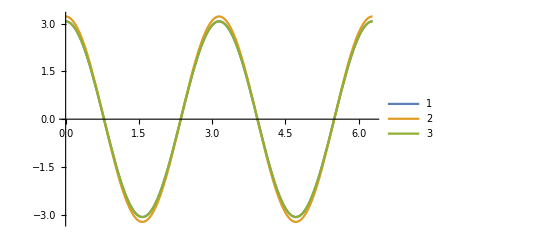

```mathematica
bmu=1;bJ=2;
t2=1/2 (BesselI[0,2]+2 BesselI[1,2]+BesselI[2,2]) Cos[2 theta1]
Plot[{t2,t2*1.05,H1nNumerical[bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
```

#### H1c

```mathematica
H1nCNumerical[n_,bJ_,bmu_,theta1_]:=NIntegrate[Cos[n theta2]*Exp[bJ Cos[theta1-theta2]] (Qy1-bmu^2(Sin[theta1]+Sin[theta2])^2),{theta2,0,2Pi}]/Pi
```

```mathematica
bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
```

bmu = 0.416893 ,bJ= 2.59718

```mathematica
A[n_]:=1/(2 BesselI[0,bJ])bmu^2 (4 BesselI[1,bJ] BesselI[n,bJ] Cos[n theta1]+BesselI[0,bJ] (BesselI[-2+n,bJ] Cos[(-2+n) theta1]+2 BesselI[n,bJ] Cos[2 theta1] Cos[n theta1]+BesselI[2+n,bJ] Cos[(2+n) theta1]+4 BesselI[-1+n,bJ] Sin[theta1] Sin[(-1+n) theta1]-4 BesselI[1+n,bJ] Sin[theta1] Sin[(1+n) theta1]))
```

```mathematica
t1=Sum[H1c[1,j,theta1],{j,0,10}];
t3=Sum[H1c[3,j,theta1],{j,0,10}];
t5=Sum[H1c[5,j,theta1],{j,0,10}];
```

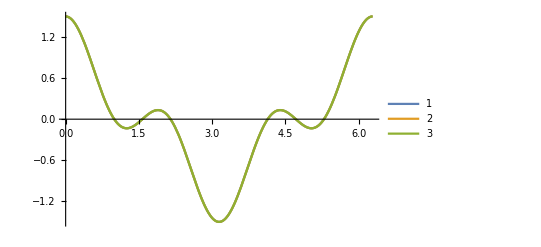

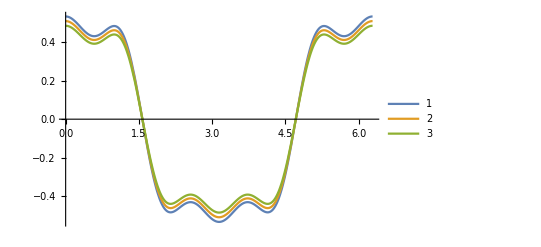

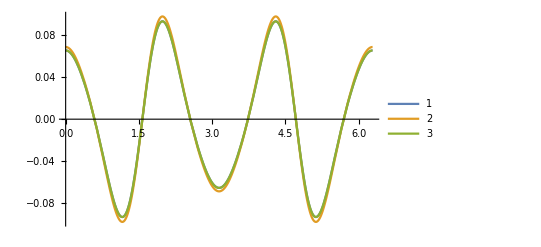

```mathematica
Plot[{t1,A[1],H1nCNumerical[1,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{t3*1.10,A[3]*1.05,H1nCNumerical[3,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{t5,A[5]*1.05,H1nCNumerical[5,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
```

#### H1s

```mathematica
bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
```

bmu = 7.10784 ,bJ= 4.53077

```mathematica
H1nsNumerical[n_,bJ_,bmu_,theta1_]:=NIntegrate[Sin[n theta2]*Exp[bJ Cos[theta1-theta2]] (Qy1-bmu^2(Sin[theta1]+Sin[theta2])^2),{theta2,0,2Pi}]/Pi
```

```mathematica
A[n_]:=1/(2 BesselI[0,bJ])bmu^2 (4 BesselI[1,bJ] BesselI[n,bJ] Sin[n theta1]+BesselI[0,bJ] (-4 BesselI[-1+n,bJ] Cos[(-1+n) theta1] Sin[theta1]+4 BesselI[1+n,bJ] Cos[(1+n) theta1] Sin[theta1]+BesselI[-2+n,bJ] Sin[(-2+n) theta1]+2 BesselI[n,bJ] Sin[n theta1]-4 BesselI[n,bJ] Sin[theta1]^2 Sin[n theta1]+BesselI[2+n,bJ] Sin[(2+n) theta1]));
```

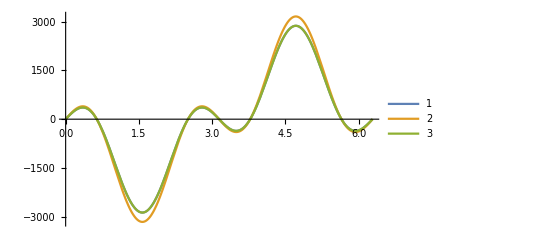

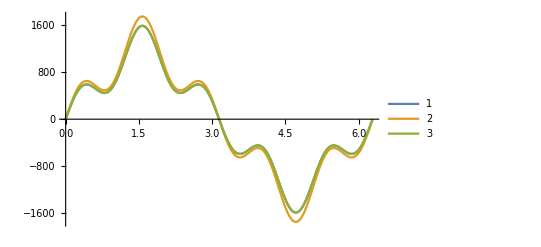

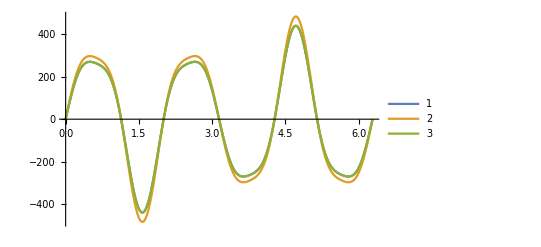

```mathematica
Plot[{A[1],A[1]*1.1,H1nsNumerical[1,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{A[3],A[3]*1.1,H1nsNumerical[3,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{A[5],A[5]*1.1,H1nsNumerical[5,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
```

### test for A1ns

#### A1cyn0 and dA1cyn0

9.59048

3.0768

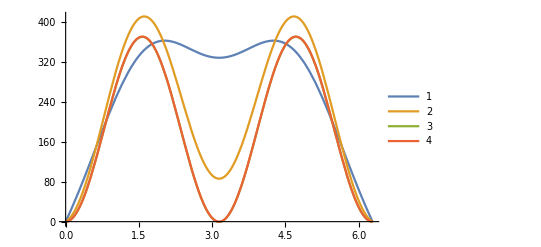

```mathematica
(*bmu=RandomReal[{1,10}]
bJ=RandomReal[{1,10}]
A1cyn0=1/4 bmu^2 (BesselI[0,bJ]+2 BesselI[1,bJ]+BesselI[2,bJ]) Sin[theta1]^2;
s1=Sum[A1c[0,j,theta1],{j,0,1}];
s5=Sum[A1c[0,j,theta1],{j,0,5}];
s10=Sum[A1c[0,j,theta1],{j,0,10}];
Plot[{s1,s5,s10,A1cyn0},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

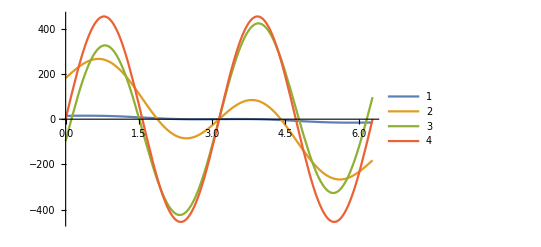

```mathematica
(*dA1cyn0=1/4 bmu^2 (BesselI[0,bJ]+2 BesselI[1,bJ]+BesselI[2,bJ]) Sin[2 theta1];
s1=Sum[dA1c[0,j,theta1],{j,0,1}];
s5=Sum[dA1c[0,j,theta1],{j,0,5}];
s10=Sum[dA1c[0,j,theta1],{j,0,10}];
Plot[{s1,s5,s10,dA1cyn0},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

#### A1cyn and dA1cyn

```mathematica
(*bmu=RandomReal[{1,10}]
bJ=RandomReal[{1,10}]*)
```

2.62901

7.83994

```mathematica
(*A1cyn[n_]:=1/(4 n^2)bmu^2 ((n^2 BesselI[-2+n,bJ] (-Cos[(-2+n) theta1]+Cosh[n theta1]))/(2+(-2+n) n)-(4 bJ (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Cos[n theta1]+2 n^2 (2+(-2+n) n) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Cos[(2+n) theta1]+bJ n^2 (2+n (2+n)) BesselI[0,bJ] (bJ BesselI[n,bJ] (Cos[(-2+n) theta1]+Cosh[n theta1])+2 BesselI[-1+n,bJ] (bJ Cos[(-2+n) theta1]+(-1+n) Cosh[n theta1])))/(bJ^2 (4+n^4) BesselI[0,bJ]))*)
```

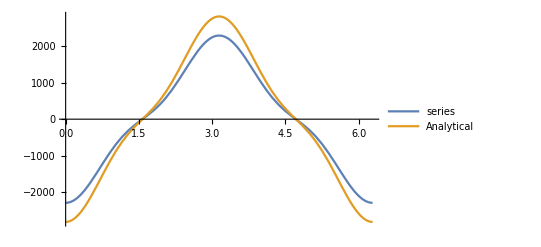

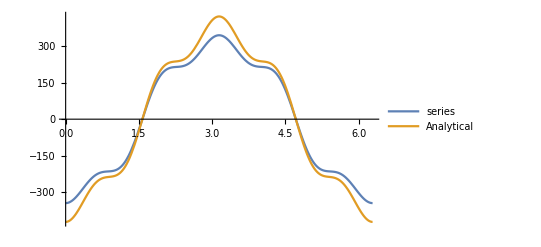

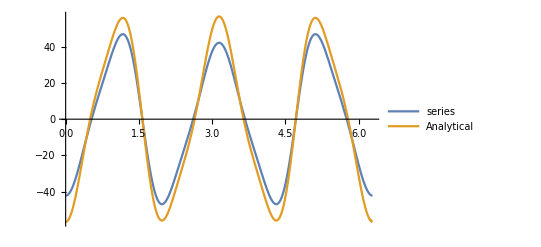

```mathematica
(*Plot[{Sum[A1c[1,j,theta1],{j,0,10}],A1cyn[1]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A1c[3,j,theta1],{j,0,10}],A1cyn[3]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A1c[5,j,theta1],{j,0,10}],A1cyn[5]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
*)
```

```mathematica
(*dA1cyn[n_]:=1/4 bmu^2 (((-2+n) BesselI[-2+n,bJ] Sin[(-2+n) theta1])/(2+(-2+n) n)+1/(bJ^2 n (4+n^4) BesselI[0,bJ])(bJ (bJ n (-4-2 n+n^3) BesselI[0,bJ] (2 BesselI[-1+n,bJ]+BesselI[n,bJ]) Sin[(-2+n) theta1]+4 (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Sin[n theta1])+2 n (4-2 n+n^3) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Sin[(2+n) theta1]))*)
```

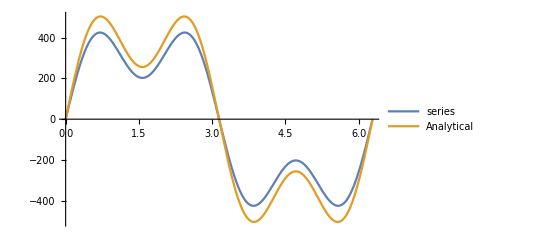

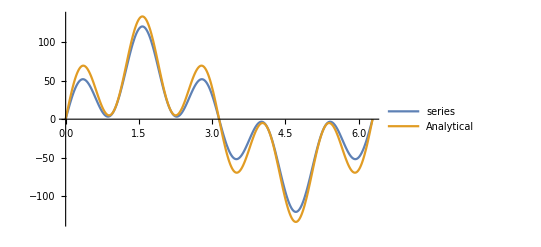

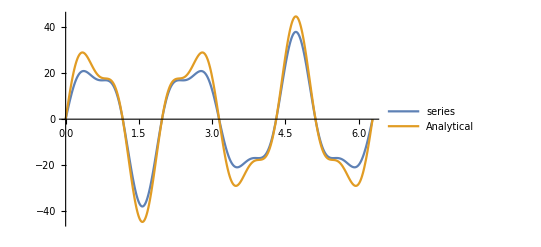

```mathematica
(*Plot[{Sum[dA1c[1,j,theta1],{j,0,10}],dA1cyn[1]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[dA1c[3,j,theta1],{j,0,10}],dA1cyn[3]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[dA1c[5,j,theta1],{j,0,10}],dA1cyn[5]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]*)
```

#### A1syn and dA1syn

```mathematica
(*bmu=RandomReal[{1,10}]
bJ=RandomReal[{1,10}]*)
```

1.27432

7.65271

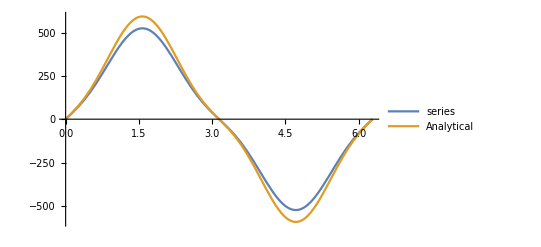

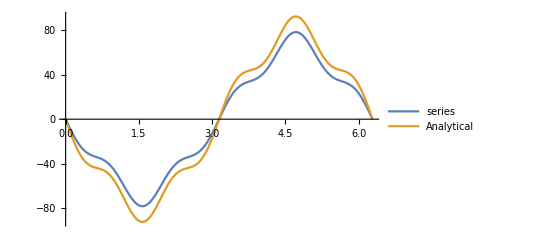

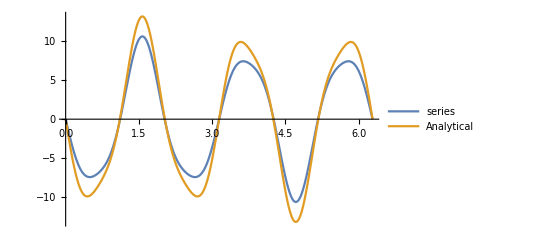

```mathematica
(*A1syn[n_]:=(bmu^2 (-bJ n^2 (2+n (2+n)) BesselI[0,bJ] ((-1+bJ+n) BesselI[-1+n,bJ]+bJ BesselI[n,bJ]) Sin[(-2+n) theta1]-2 bJ (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Sin[n theta1]-n^2 (2+(-2+n) n) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Sin[(2+n) theta1]))/(2 bJ^2 n^2 (4+n^4) BesselI[0,bJ])
Plot[{Sum[A1s[1,j,theta1],{j,0,10}],A1syn[1]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A1s[3,j,theta1],{j,0,10}],A1syn[3]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A1s[5,j,theta1],{j,0,10}],A1syn[5]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]*)
```

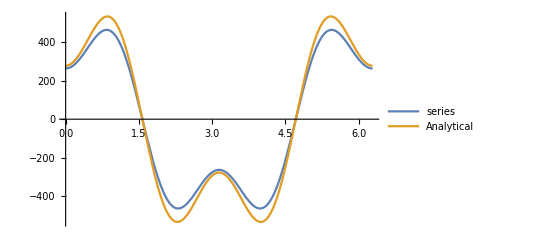

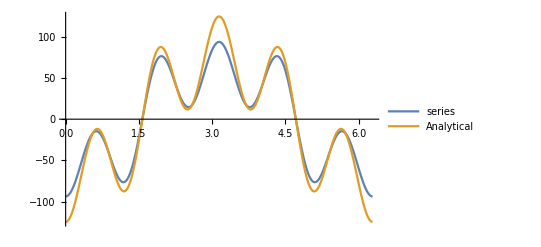

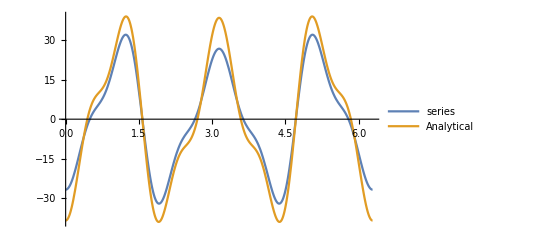

```mathematica
(*dA1syn[n_]:=1/4 bmu^2 (-(((-2+n) BesselI[-2+n,bJ] Cos[(-2+n) theta1])/(2+(-2+n) n))+1/(bJ^2 n (4+n^4) BesselI[0,bJ])(bJ (-bJ n (-4-2 n+n^3) BesselI[0,bJ] (2 BesselI[-1+n,bJ]+BesselI[n,bJ]) Cos[(-2+n) theta1]-4 (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Cos[n theta1])-2 n (4-2 n+n^3) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Cos[(2+n) theta1]));
Plot[{Sum[dA1s[1,j,theta1],{j,0,10}],dA1syn[1]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[dA1s[3,j,theta1],{j,0,10}],dA1syn[3]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[dA1s[5,j,theta1],{j,0,10}],dA1syn[5]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]*)
```

### test for pv1ns

```mathematica
pv11[bJx_,bmux_,xi_,xj_]:=Release[Sum[dA1s[n,j,theta1]Sin[n theta2]+dA1c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,nmax},{j,0,jmax}]]
pv21[bJx_,bmux_,xi_,xj_]:=Release[Sum[n A1s[n,j,theta1]Cos[n theta2]-n A1c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,1,nmax},{j,0,jmax}]]
```

```mathematica
pvy11[theta1_,theta2_,nmax_]:=Sum[dAys1[n,theta1]Sin[n theta2]+dAyc1[n,theta1]Cos[n theta2],{n,0,nmax}]
pvy21[theta1_,theta2_,nmax_]:=Sum[n Ays1[n,theta1]Cos[n theta2]-n Ayc1[n,theta1]Sin[n theta2],{n,1,nmax}]
pvy11n[theta1_,theta2_,nmax_]:=dAys1[n,theta1]Sin[n theta2]+dAyc1[n,theta1]Cos[n theta2]
pvy21n[theta1_,theta2_,nmax_]:=n Ays1[n,theta1]Cos[n theta2]-n Ayc1[n,theta1]Sin[n theta2]
```

1.98734

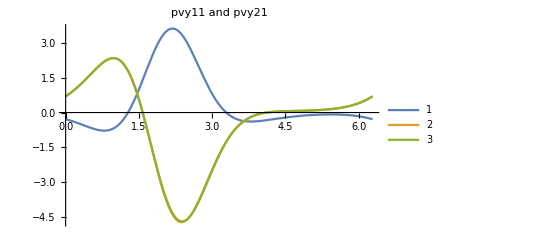

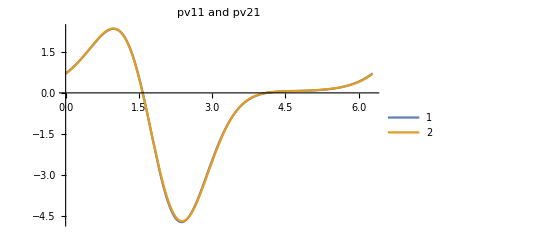

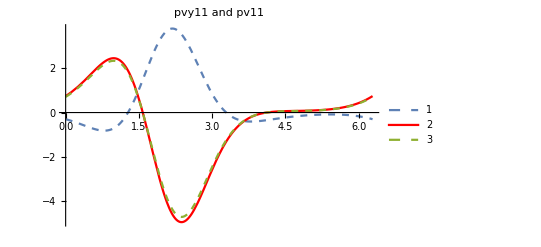

```mathematica
myt2=RandomReal[{0,2Pi}]
bJ=1.0;
bmu=1.0;
nmax=RandomInteger[{1,3}];
nmax=3;
jmax=10;
Plot[{pvx11[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]],pvy11[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]],pvy21[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic,PlotLabel->"pvy11 and pvy21"]
Plot[{pv11[1.0,1.0,theta2,myt2]Exp[Cos[theta2-myt2]],pv21[1.0,1.0,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic,PlotLabel->"pv11 and pv21"]
Plot[{pvx11[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]]*1.05,pvy11[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]]*1.05,pv11[1.0,1.0,theta2,myt2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic,PlotLabel->"pvy11 and pv11",PlotStyle->{Dashed,Red}]
```